```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Edetect={1 10^-8,2.5 10^-8,1 10^-7,2 10^-7,3 10^-7,4 10^-7,5 10^-7,6 10^-7,8 10^-7,1 10^-6,3.16 10^-6,1 10^-5,1 10^-4,1 10^-3,1 10^-2};
pointfiles={
"prevLPemissionPoints_e01.tst",
"prevLPemissionPoints_e02.tst",
"prevLPemissionPoints_e03.tst",
"prevLPemissionPoints_e04.tst",
"prevLPemissionPoints_e05.tst",
"prevLPemissionPoints_e06.tst",
"prevLPemissionPoints_e07.tst",
"prevLPemissionPoints_e08.tst",
"prevLPemissionPoints_e09.tst",
"prevLPemissionPoints_e10.tst",
"prevLPemissionPoints_e11.tst",
"prevLPemissionPoints_e12.tst",
"prevLPemissionPoints_e13.tst",
"prevLPemissionPoints_e14.tst",
"prevLPemissionPoints_e15.tst"
};
tracefiles={
"prevLPemissionPoints_e01_traces.tst",
"prevLPemissionPoints_e02_traces.tst",
"prevLPemissionPoints_e03_traces.tst",
"prevLPemissionPoints_e04_traces.tst",
"prevLPemissionPoints_e05_traces.tst",
"prevLPemissionPoints_e06_traces.tst",
"prevLPemissionPoints_e07_traces.tst",
"prevLPemissionPoints_e08_traces.tst",
"prevLPemissionPoints_e09_traces.tst",
"prevLPemissionPoints_e10_traces.tst",
"prevLPemissionPoints_e11_traces.tst",
"prevLPemissionPoints_e12_traces.tst",
"prevLPemissionPoints_e13_traces.tst",
"prevLPemissionPoints_e14_traces.tst",
"prevLPemissionPoints_e15_traces.tst"
};
mapfiles={
"LPemissionMap_e01.tst",
"LPemissionMap_e02.tst",
"LPemissionMap_e03.tst",
"LPemissionMap_e04.tst",
"LPemissionMap_e05.tst",
"LPemissionMap_e06.tst",
"LPemissionMap_e07.tst",
"LPemissionMap_e08.tst",
"LPemissionMap_e09.tst",
"LPemissionMap_e10.tst",
"LPemissionMap_e11.tst",
"LPemissionMap_e12.tst",
"LPemissionMap_e13.tst",
"LPemissionMap_e14.tst",
"LPemissionMap_e15.tst"
};
rMoon=1737;
aMoon=0.3844 10^6;
mMoon=0.07346 10^24;
mEarth=5.9724 10^24;
rSOImoon=aMoon(mMoon/mEarth)^(2/5);
p=250;
{vp,vv}=Options[Graphics3D,{ViewPoint,ViewVertical}][[All,2]];
a=Table[ReadList[pointfiles[[i]],Number,RecordLists->True],{i,1,Length[pointfiles],1}];
b=Table[Partition[ReadList[tracefiles[[i]],Number,RecordLists->True],11],{i,1,Length[tracefiles],1}];
c=Table[ReadList[mapfiles[[i]],Number,RecordLists->True],{i,1,Length[mapfiles],1}];
```

```mathematica
origin={0,0,0};
Dhat=a[[1,1,9;;11]];
Nhat=a[[1,1,12;;14]];
Fhat=a[[1,1,15;;17]];
Rsat=a[[1,1,3;;5]];
rView=Norm[Rsat];
r1s=a[[;;,;;,5;;7]];
v1s=a[[;;,;;,8;;10]];
arrDs=a[[;;,;;,1;;3]];
v2s=b[[;;,;;,11,5;;7]];
traces=b[[;;,;;,;;,2;;4]];
lenA=Table[Length[a[[i]]],{i,1,Length[a]}];
lenB=Table[Length[b[[i]]],{i,1,Length[b]}];
trips=Flatten[traces,2];
rMaxs=Table[Max[Table[Norm[Flatten[traces[[j]],1][[i]]],{i,1,lenB[[j]]}]],{j,1,Length[tracefiles],1}];
```

```mathematica
Manipulate[
If[j>k,k=j];
If[k>lenB[[En]],k=lenB[[En]]];
If[r>rMaxs[[En]],r=rMaxs[[En]]];
Grid[{{
Show[ListPointPlot3D[
{
Table[a[[En,1,3;;5]]+p a[[En,i,1;;3]],{i,2,Length[a[[En,2;;]]],1}],
a[[En,2;;,5;;7]]
},
PlotStyle->{Directive[Gray,PointSize[0.001]],Directive[Black,PointSize[0.004]]},PlotRange->Table[{-r,r},3],BoxRatios->1,ImageSize->720,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv],PlotLabel->"En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15r Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9r{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}],
Graphics3D[{Green,Line[traces[[En,j;;k]]]}],
Table[Graphics3D[{Orange,Arrowheads[.01],Arrow[{r1s[[En,i]],r1s[[En,i]]+.05r v1s[[En,i]]}]}],{i,j+1,k+1,1}]
],
Grid[{
{Show[ListPointPlot3D[
a[[En,2;;,1;;3]],
PlotStyle->Directive[Gray,PointSize[0.007]],PlotRange->{-1,1},BoxRatios->1,ImageSize->360,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]],
Graphics3D[{Black,Arrowheads[.02],Arrow[{origin,Dhat}]}],
Graphics3D[{Blue,Arrowheads[.02],Arrow[{origin,Nhat}]}],
Graphics3D[{Red,Arrowheads[.02],Arrow[{origin,Fhat}]}],
Table[Graphics3D[{Darker[Green],PointSize[0.01],Point[arrDs[[En,i]]]}],{i,j+1,k+1,1}],
Table[Graphics3D[{Darker[Green],Arrow[{arrDs[[En,i]],origin}]}],{i,j+1,k+1,1}],
Table[Graphics3D[{Green,Arrow[{-v2s[[En,i]],origin}]}],{i,j,k,1}]
]},
{Show[ListPointPlot3D[
a[[En,2;;,5;;7]],
PlotStyle->{Directive[Black,PointSize[0.007]]},PlotRange->Table[1.25rMoon{-1,1},3],BoxRatios->1,ImageSize->360,ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.03],Arrow[{origin,1.2rMoon{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}],
Table[Graphics3D[{Orange,Arrowheads[.02],Arrow[{r1s[[En,i]],r1s[[En,i]]+.1rMoon v1s[[En,i]]}]}],{i,j+1,k+1,1}]
]}
},Frame->{{False,False},{False,True}}]
}},Frame->All],
{{En,1},1,Length[lenA],1,Appearance->{"Open"}},
{{j,1},1,lenB[[En]],1,Appearance->{"Open"}},
{{k,Max[lenB]},j,Max[lenB],1,Appearance->{"Open"}},
{{r,rSOImoon},rView,rSOImoon,(rSOImoon-Norm[Rsat])/100,Appearance->{"Open"}},
ContinuousAction->False,ControlPlacement->Left
]
```

```mathematica
padding={{72,48},{36,20}};
tofEnpairs=Table[Partition[Riffle[a[[En,2;;,4]],a[[En,2;;,11]]/1000],2],{En,1,Length[a],1}];
tofDpairs=Table[Partition[Riffle[a[[En,2;;,4]],a[[En,2;;,12]]],2],{En,1,Length[a],1}];
Manipulate[
Overlay[{
ListLogLogPlot[tofEnpairs[[En]],ImageSize->Large,PlotStyle->Blue,Frame->{{True,False},{True,True}},FrameTicks->{{True,False},{True,False}},FrameStyle->{{Blue,None},{Black,Black}},FrameLabel->{{"En [keV]",None},{"tof [s]","En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"}},ImagePadding->padding],
ListLogLogPlot[tofDpairs[[En]],ImageSize->Large,PlotStyle->Red,Frame->{{False,True},{False,False}},FrameTicks->True,FrameStyle->{{None,Red},{None,None}},FrameLabel->{{None,"D-factor"},{None,None}},ImagePadding->padding]
},Alignment->Center],
{En,1,Length[a],1,Appearance->{"Open"}}]
```

```mathematica
EnIpairs=Table[Partition[Riffle[a[[En,2;;,11]]/1000,2376/(a[[En,2;;,12]] ⅇ^(-a[[En,2;;,4]]/L))],2],{En,1,Length[a],1}];
Manipulate[
If[m1≥m2,m2=m1+1];
ListLogLogPlot[EnIpairs[[En]]/.L->Ln,ImageSize->Large,PlotRange->{All,{10^m1,10^m2}},PlotStyle->Blue,Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Black,FrameLabel->{{"I [n-surface per n-detector]",None},{"En [MeV]","En at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"}}],
{En,1,Length[a],1,Appearance->{"Open"}},
{{Ln,881},875,895,0.5,Appearance->{"Open"}},
{{m1,9},1,60,1,Appearance->{"Open"}},
{{m2,15},1,60,1,Appearance->{"Open"}},
ControlPlacement->Right]
```

```mathematica
latTicks=Table[i,{i,-90,90,15}];
lonTicks=Table[i,{i,-180,180,30}];
spread=2.5;
LonLatRect5[xy_]:=Rectangle[xy-spread,xy+spread];
```

```mathematica
CmapTriplets=Table[c[[En,2;;,{2,1,18}]],{En,1,Length[c],1}];
CmapTriplets[[;;,;;,3]]=Table[CmapTriplets[[En,;;,3]]/Max[CmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Cmap2lists=Table[Table[{CmapTriplets[[En,i,1;;2]]},{i,1,Length[CmapTriplets[[En,;;,3]]],1}],{En,1,Length[CmapTriplets],1}];
CmapColors=Table[Table[ColorData["Rainbow"][CmapTriplets[[En,i,3]]],{i,1,Length[CmapTriplets[[En,;;,3]]],1}],{En,1,Length[CmapTriplets],1}];
CmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE NUMBER OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{CmapColors[[En,i]],Point[CmapVecs[[En,i]]]},{i,1,Length[CmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],CmapColors[[En,i]],LonLatRect5[Flatten[Cmap2lists[[En,i]]]]}],{i,1,Length[Cmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[CmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
FmapTriplets=Table[c[[En,2;;,{2,1,6}]],{En,1,Length[c],1}];
FErrmapTriplets=Table[c[[En,2;;,{2,1,7}]],{En,1,Length[c],1}];
FErrmapTriplets[[;;,;;,3]]=100(Abs[FErrmapTriplets[[;;,;;,3]]]/FmapTriplets[[;;,;;,3]]);
Table[Mean[FmapTriplets[[En,;;,3]]],{En,1,Length[c],1}]
FmapTriplets[[;;,;;,3]]=Table[FmapTriplets[[En,;;,3]]/Max[FmapTriplets[[En,;;,3]]],{En,1,Length[c],1}]
```

{0.000968054,0.000589275,0.00142653,0.00172117,0.0018018,0.00184162}

{{0.0055003,0.00987258,0.00971246,0.00959547,0.00909162,0.0285797,0.00805366,0.00958745,0.0130242,0.00999738,0.00923271,0.00390799,2.95611×10^-8,2.55554×10^-7,0.00613226,0.00842654,0.00519185,0.000805435,0.000751232,0.00078395,0.000830419,0.000862323,0.000860486,0.000825064,0.000781439,0.00075221,0.000814226,0.00526626,0.0118501,0.00789203,2.55434×10^-7,1.07097×10^-8,1.36134×10^-6,3.71003×10^-6,8.41819×10^-7,0.00183987,0.00914263,0.00330478,0.00055119,0.000538123,0.000601859,0.000703268,0.000826725,0.000938005,0.00100829,0.00100447,0.000933838,0.000817018,0.000694254,0.000593823,0.000535167,0.000558258,0.00342368,0.00866014,0.00195652,1.02873×10^-6,3.72908×10^-6,1.15716×10^-6,6.15961×10^-9,4.583×10^-6,8.43008×10^-6,4.3271×10^-6,2.5959×10^-7,0.0114171,0.00664723,0.000470397,0.000379923,0.00040242,0.000473628,0.000590696,0.000744553,0.000924535,0.00109215,0.00118646,0.00118759,0.0010742,0.000910219,0.0007311,0.000577958,0.000467255,0.000397202,0.000380924,0.000488175,0.00767823,0.00299711,3.67527×10^-7,4.78548×10^-6,8.40124×10^-6,4.24251×10^-6,2.56097×10^-7,8.55981×10^-6,0.0000118558,8.22678×10^-6,2.57588×10^-6,7.73799×10^-10,0.00378702,0.00460647,0.00032258,0.000274109,0.000292791,0.000346156,0.000439349,0.00056949,0.00074486,0.000942129,0.00113238,0.00123712,0.00123676,0.00111568,0.000924863,0.000727858,0.000557665,0.000430627,0.000340263,0.000290549,0.000275752,0.00032832,0.00377285,0.00357321,5.41731×10^-9,2.95712×10^-6,8.73043×10^-6,0.000012098,8.09059×10^-6,1.26833×10^-7,6.25722×10^-7,0.0000119316,0.0000152068,0.0000121701,6.75972×10^-6,4.66768×10^-7,0.00523539,0.00450448,0.000241393,0.000202507,0.000208854,0.000241814,0.00029995,0.000387821,0.000514443,0.000672109,0.00085355,0.00101545,0.00111372,0.00111155,0.00100585,0.000839267,0.000661347,0.000501017,0.000381274,0.000293774,0.000237766,0.000207376,0.000201915,0.000247631,0.00305249,0.00293265,6.15794×10^-7,7.06024×10^-6,0.0000124032,0.0000152229,0.000011216,3.50457×10^-7,7.05876×10^-7,0.0000147561,0.000018712,0.0000162774,0.0000111515,2.35109×10^-6,0.00428465,0.00202209,0.00019132,0.000151821,0.000150182,0.000166978,0.000198519,0.000250067,0.000322989,0.000424816,0.000550483,0.000690807,0.000815672,0.000883531,0.000879885,0.000803485,0.000677254,0.000542517,0.000415224,0.000315812,0.000245136,0.000194655,0.000163766,0.000148751,0.000152509,0.000196632,0.00329274,0.00912739,2.74391×10^-6,0.000011748,0.0000164315,0.0000188163,0.0000137426,3.88933×10^-7,5.87628×10^-7,0.0000167335,0.0000223858,0.0000207314,0.0000167293,5.51423×10^-6,1.1791×10^-8,0.00303795,0.00226309,0.000158963,0.000118047,0.000109811,0.000114911,0.000131531,0.000158478,0.0001988,0.000255314,0.000328108,0.000417027,0.000510458,0.000592176,0.00063767,0.00063577,0.00058466,0.000502608,0.000409899,0.000321973,0.000250594,0.000195202,0.000156249,0.000129899,0.000114306,0.000109957,0.000119297,0.000163822,0.0024854,0.0020652,3.21124×10^-8,6.51188×10^-6,0.0000171198,0.0000210012,0.0000224654,0.0000156388,2.71689×10^-7,3.17473×10^-7,0.0000186163,0.0000269588,0.0000263847,0.0000238821,0.0000101971,1.21593×10^-7,0.00205345,0.00217026,0.000135637,0.0000940609,0.000082705,0.0000825505,0.0000889633,0.00010256,0.000121968,0.000151822,0.000191398,0.000240475,0.000299201,0.00035778,0.000405469,0.000431626,0.000432466,0.000402373,0.000351377,0.000293109,0.000236999,0.000187488,0.000149817,0.00012024,0.000100589,0.0000880977,0.0000822726,0.0000829425,0.0000951403,0.000141274,0.00217012,0.00162342,2.49662×10^-7,0.0000116506,0.0000244262,0.0000262892,0.0000272824,0.0000172915,1.04857×10^-7,1.27711×10^-7,0.0000205695,0.0000333253,0.0000336477,0.0000343527,0.0000166543,1.86208×10^-7,0.00150159,0.00172776,0.000119482,0.0000775599,0.0000643252,0.0000606278,0.0000620983,0.0000674937,0.0000782338,0.0000927273,0.000112483,0.000139151,0.000170264,0.000204681,0.000239879,0.000268261,0.000283321,0.000281934,0.000266941,0.000236626,0.000202468,0.000167086,0.000136822,0.000110412,0.000091524,0.0000768222,0.0000670974,0.0000618452,0.0000605043,0.0000648006,0.0000785124,0.000125172,0.00196955,0.0013257,3.70308×10^-7,0.0000182634,0.0000349254,0.0000337893,0.0000330528,0.000018508,2.75109×10^-9,1.50559×10^-8,0.000023524,0.0000421348,0.0000446629,0.0000533356,0.0000241571,3.57863×10^-8,0.0292135,0.00205008,0.000105233,0.0000647943,0.000051725,0.0000460908,0.0000447702,0.0000469966,0.0000508698,0.000058137,0.000068292,0.0000811549,0.0000973845,0.000116896,0.000137378,0.000157108,0.000172628,0.000180629,0.000181064,0.000172062,0.000155134,0.000135473,0.000114959,0.0000969299,0.000080243,0.0000674367,0.0000570714,0.000050558,0.0000463147,0.000044743,0.0000462761,0.0000519525,0.0000660649,0.000109875,0.00322322,0.0071081,1.74307×10^-7,0.0000273567,0.0000531185,0.0000447275,0.0000422954,0.000020672,0.000029479,0.0000568415,0.0000640802,0.00014424,0.0000337812,0.006466,0.00313193,0.0000889668,0.0000544147,0.0000421065,0.0000359358,0.0000337482,0.0000331337,0.0000347288,0.0000376158,0.0000425098,0.0000484251,0.0000574686,0.0000668607,0.0000784173,0.0000897553,0.000101347,0.00010924,0.000113658,0.000114271,0.000109061,0.0000997887,0.0000894335,0.0000769828,0.0000667414,0.0000567918,0.0000481365,0.0000419305,0.0000372809,0.0000342549,0.0000331564,0.0000333382,0.000035909,0.0000421464,0.0000554846,0.00009336,0.00148658,0.00194434,0.0000687681,0.000142432,0.0000637675,0.0000567541,0.000025706,9.55789×10^-9,0.0000452446,0.0000876775,0.000190956,0.000487439,0.000126171,0.0000409884,0.00282262,0.000940336,0.0000722711,0.0000452802,0.0000340601,0.000028392,0.0000253682,0.0000244489,0.0000244166,0.0000252706,0.0000272194,0.0000303985,0.0000345583,0.0000391723,0.0000452817,0.0000516871,0.0000583132,0.0000643928,0.000069023,0.0000715678,0.0000714966,0.0000686134,0.0000634434,0.0000575244,0.0000509143,0.0000446273,0.0000389522,0.0000340755,0.0000299789,0.000027156,0.0000251063,0.000024122,0.0000242393,0.0000256537,0.0000285542,0.0000345393,0.0000458755,0.0000751549,0.00149314,0.0023409,0.000126794,0.000513642,0.000236544,0.0000874152,0.0000395937,0.0000864501,4.98318×10^-8,9.30806×10^-7,0.0000973664,0.000183967,0.00168197,0.00105898,0.000980125,0.00240012,0.000132653,0.0000554183,0.0000363906,0.0000274449,0.0000223872,0.0000197792,0.0000183229,0.0000176335,0.0000174443,0.0000179447,0.0000195155,0.0000211563,0.0000237045,0.0000266193,0.0000300159,0.0000335065,0.0000373061,0.0000401055,0.0000425433,0.0000441382,0.0000440812,0.0000424998,0.0000401364,0.0000366928,0.0000332916,0.0000297576,0.0000261665,0.0000233624,0.000020952,0.00001914,0.0000180157,0.0000174199,0.0000174526,0.0000183208,0.0000197576,0.0000226977,0.0000276555,0.0000367682,0.000057244,0.000204222,0.00229647,0.00104592,0.000590699,0.00128038,0.000177453,0.00373996,0.00110503,0.0000183068,0.0000346677,0.0010285,0.0034365,0.00137492,0.0000613186,0.00112062,0.00175692,0.00160277,0.0000678066,0.0000398412,0.0000279748,0.0000215372,0.0000174929,0.000015213,0.0000136105,0.0000128074,0.0000123772,0.0000123093,0.0000126812,0.0000133326,0.0000145062,0.0000158524,0.000017564,0.000019494,0.0000211496,0.0000233479,0.0000246838,0.0000260035,0.0000266134,0.0000267692,0.0000261657,0.0000248542,0.0000232129,0.000021008,0.0000190406,0.0000173883,0.0000156168,0.0000141793,0.0000131366,0.0000125247,0.0000122592,0.0000123533,0.0000127898,0.0000137171,0.0000152809,0.000017757,0.0000219842,0.0000286268,0.0000410056,0.0000712369,0.000913319,0.00228273,0.00134771,0.000217989,0.00163366,0.0192487,1.,0.0586292,0.0373314,0.000113226,0.00152389,0.0014347,0.00214346,0.000593361,0.0000669126,0.0000401899,0.0000276287,0.0000207398,0.0000163791,0.0000136968,0.000011555,0.0000101684,9.22112×10^-6,8.72731×10^-6,8.42893×10^-6,8.36618×10^-6,8.51831×10^-6,8.92858×10^-6,9.46767×10^-6,0.0000104394,0.0000110402,0.0000121819,0.0000131886,0.0000141127,0.0000149231,0.0000157187,0.0000157044,0.0000158976,0.0000154776,0.0000148962,0.0000142505,0.0000130331,0.0000120735,0.0000109274,0.0000101619,9.4845×10^-6,8.93291×10^-6,8.47196×10^-6,8.31909×10^-6,8.363×10^-6,8.76949×10^-6,9.33406×10^-6,0.0000103286,0.0000115339,0.0000136487,0.0000165188,0.0000208116,0.000028189,0.0000410542,0.0000693089,0.000682789,0.00401029,0.00177239,0.00149591,0.000139074,0.00547001,0.00197243,0.0001019,0.00013692,0.00191965,0.00354192,0.00272016,0.00235793,0.00179184,0.00191627,0.00315799,0.00227455,0.000137313,0.0000707666,0.0000460486,0.0000322152,0.0000238372,0.0000183223,0.0000145905,0.00001192,9.86637×10^-6,8.47098×10^-6,7.47616×10^-6,6.59696×10^-6,6.1284×10^-6,5.78856×10^-6,5.58268×10^-6,5.48054×10^-6,5.60769×10^-6,5.71489×10^-6,6.02099×10^-6,6.30459×10^-6,6.71453×10^-6,7.25314×10^-6,7.78472×10^-6,8.22693×10^-6,8.64264×10^-6,8.97412×10^-6,9.10784×10^-6,9.17462×10^-6,8.92879×10^-6,8.53071×10^-6,8.18828×10^-6,7.74163×10^-6,7.25328×10^-6,6.69219×10^-6,6.1939×10^-6,5.8398×10^-6,5.72885×10^-6,5.46156×10^-6,5.4921×10^-6,5.53901×10^-6,5.73281×10^-6,6.06646×10^-6,6.68469×10^-6,7.45404×10^-6,8.63174×10^-6,0.0000100551,0.0000120981,0.0000145475,0.0000185305,0.0000241593,0.0000325435,0.0000467975,0.0000719531,0.000142896,0.00161749,0.00165124,0.00188897,0.00190765,0.00233855,0.00752128,0.000032282,1.6326×10^-8,0.0000379213,0.000069737,0.0000652058,0.0000546137,0.0000456252,0.0000378599,0.0000310984,0.0000253489,0.0000208041,0.0000169496,0.0000137991,0.0000115046,9.58458×10^-6,8.02275×10^-6,6.81278×10^-6,5.82368×10^-6,5.12334×10^-6,4.6288×10^-6,4.16329×10^-6,3.85933×10^-6,3.60414×10^-6,3.47336×10^-6,3.33373×10^-6,3.34805×10^-6,3.37611×10^-6,3.54549×10^-6,3.58253×10^-6,3.81348×10^-6,4.01776×10^-6,4.23508×10^-6,4.44284×10^-6,4.62286×10^-6,4.82966×10^-6,4.91916×10^-6,4.89388×10^-6,4.75039×10^-6,4.71607×10^-6,4.50485×10^-6,4.37458×10^-6,3.97371×10^-6,3.79756×10^-6,3.61583×10^-6,3.44547×10^-6,3.34777×10^-6,3.29866×10^-6,3.29445×10^-6,3.39236×10^-6,3.59849×10^-6,3.85244×10^-6,4.13117×10^-6,4.64854×10^-6,5.19715×10^-6,5.94409×10^-6,6.84848×10^-6,8.14326×10^-6,9.61587×10^-6,0.000011577,0.000014031,0.0000171053,0.0000210794,0.0000259943,0.0000313179,0.0000380856,0.0000460757,0.0000551695,0.0000661052,0.0000687085,8.30915×10^-7,0.0000133397,0.0000221261,0.0000217739,0.0000186662,0.0000158592,0.0000134854,0.0000115652,9.79253×10^-6,8.30889×10^-6,7.08968×10^-6,6.05034×10^-6,5.19369×10^-6,4.56925×10^-6,3.99177×10^-6,3.50435×10^-6,3.07315×10^-6,2.80117×10^-6,2.48963×10^-6,2.26032×10^-6,2.10376×10^-6,1.95225×10^-6,1.85176×10^-6,1.81711×10^-6,1.83683×10^-6,1.85794×10^-6,1.93379×10^-6,2.00817×10^-6,2.10435×10^-6,2.19054×10^-6,2.22131×10^-6,2.29532×10^-6,2.33976×10^-6,2.337×10^-6,2.31119×10^-6,2.23874×10^-6,2.16004×10^-6,2.10556×10^-6,1.971×10^-6,1.87581×10^-6,1.83503×10^-6,1.84135×10^-6,1.82818×10^-6,1.84731×10^-6,1.94058×10^-6,2.0653×10^-6,2.24586×10^-6,2.51662×10^-6,2.74159×10^-6,3.09095×10^-6,3.50618×10^-6,4.01888×10^-6,4.5458×10^-6,5.31736×10^-6,6.09378×10^-6,7.17268×10^-6,8.31787×10^-6,9.87833×10^-6,0.0000116015,0.0000137114,0.0000160076,0.0000187894,0.0000220836,0.0000214306,0.0000120993,3.6013×10^-7,5.90054×10^-8,3.6523×10^-6,7.42757×10^-6,9.23785×10^-6,8.65982×10^-6,7.52748×10^-6,6.60142×10^-6,5.86855×10^-6,5.12077×10^-6,4.48387×10^-6,4.011×10^-6,3.55352×10^-6,3.13792×10^-6,2.83031×10^-6,2.54818×10^-6,2.28861×10^-6,2.10241×10^-6,1.92067×10^-6,1.75375×10^-6,1.61616×10^-6,1.52309×10^-6,1.42871×10^-6,1.36198×10^-6,1.27153×10^-6,1.24495×10^-6,1.17795×10^-6,1.14324×10^-6,1.1372×10^-6,1.11046×10^-6,1.11434×10^-6,1.12097×10^-6,1.10672×10^-6,1.10031×10^-6,1.10716×10^-6,1.12713×10^-6,1.14251×10^-6,1.18573×10^-6,1.24101×10^-6,1.27869×10^-6,1.36534×10^-6,1.45155×10^-6,1.54796×10^-6,1.64257×10^-6,1.75885×10^-6,1.93874×10^-6,2.10595×10^-6,2.31547×10^-6,2.58212×10^-6,2.80956×10^-6,3.15548×10^-6,3.55845×10^-6,4.00566×10^-6,4.53425×10^-6,5.17268×10^-6,5.8001×10^-6,6.71219×10^-6,7.68853×10^-6,8.74536×10^-6,9.08685×10^-6,7.16502×10^-6,3.12328×10^-6,1.08559×10^-9,8.72693×10^-8,1.4882×10^-6,2.67321×10^-6,3.4158×10^-6,3.83154×10^-6,3.78072×10^-6,3.38902×10^-6,3.03518×10^-6,2.7597×10^-6,2.48931×10^-6,2.27496×10^-6,2.11709×10^-6,1.94428×10^-6,1.76074×10^-6,1.64106×10^-6,1.52789×10^-6,1.43769×10^-6,1.33993×10^-6,1.26902×10^-6,1.21014×10^-6,1.15125×10^-6,1.1269×10^-6,1.07763×10^-6,1.03626×10^-6,1.03027×10^-6,1.01026×10^-6,9.91626×10^-7,9.81657×10^-7,9.94581×10^-7,1.00982×10^-6,9.93173×10^-7,1.01833×10^-6,1.02831×10^-6,1.08147×10^-6,1.12679×10^-6,1.15305×10^-6,1.20925×10^-6,1.27423×10^-6,1.35533×10^-6,1.44551×10^-6,1.53418×10^-6,1.65999×10^-6,1.78664×10^-6,1.93513×10^-6,2.10714×10^-6,2.3162×10^-6,2.52124×10^-6,2.80139×10^-6,3.07306×10^-6,3.41821×10^-6,3.78957×10^-6,3.72059×10^-6,3.3143×10^-6,2.52907×10^-6,1.23152×10^-6,2.7138×10^-8,1.89564×10^-7,5.89911×10^-7,8.77472×10^-7,1.06172×10^-6,1.13511×10^-6,1.15763×10^-6,1.19954×10^-6,1.17356×10^-6,1.15638×10^-6,1.13052×10^-6,1.05944×10^-6,9.99095×10^-7,9.50576×10^-7,9.00034×10^-7,8.40346×10^-7,8.09231×10^-7,7.66015×10^-7,7.20096×10^-7,6.86901×10^-7,6.78299×10^-7,6.38044×10^-7,6.34561×10^-7,6.19018×10^-7,6.24049×10^-7,6.40594×10^-7,6.38787×10^-7,6.70874×10^-7,6.92706×10^-7,7.2448×10^-7,7.52699×10^-7,8.12486×10^-7,8.44617×10^-7,8.9962×10^-7,9.45846×10^-7,1.00264×10^-6,1.03193×10^-6,1.10236×10^-6,1.14884×10^-6,1.1569×10^-6,1.16405×10^-6,1.16293×10^-6,1.09406×10^-6,9.86747×10^-7,8.12324×10^-7,5.44359×10^-7,1.31384×10^-7},{2.29116×10^-6,2.17617×10^-6,2.20565×10^-6,2.34287×10^-6,2.23807×10^-6,2.24524×10^-6,2.2691×10^-6,2.25636×10^-6,2.28023×10^-6,2.27189×10^-6,2.22344×10^-6,2.35253×10^-6,2.29926×10^-6,2.47516×10^-6,2.16812×10^-6,2.42858×10^-6,2.43528×10^-6,2.38575×10^-6,2.51637×10^-6,2.42525×10^-6,2.52488×10^-6,2.47983×10^-6,2.51178×10^-6,2.52939×10^-6,2.57722×10^-6,2.66798×10^-6,2.62615×10^-6,2.67965×10^-6,2.73335×10^-6,2.7895×10^-6,2.71655×10^-6,2.88606×10^-6,2.83063×10^-6,2.81668×10^-6,2.82281×10^-6,2.95712×10^-6,2.87294×10^-6,2.7674×10^-6,2.91369×10^-6,2.95064×10^-6,3.05325×10^-6,2.82302×10^-6,2.87866×10^-6,2.85695×10^-6,2.85615×10^-6,2.87997×10^-6,2.84749×10^-6,2.80652×10^-6,2.74853×10^-6,2.78099×10^-6,2.72218×10^-6,2.7446×10^-6,2.64401×10^-6,2.62405×10^-6,2.51099×10^-6,2.55032×10^-6,2.58692×10^-6,2.42371×10^-6,2.46943×10^-6,2.48187×10^-6,2.44901×10^-6,2.27144×10^-6,2.38472×10^-6,2.3156×10^-6,2.3511×10^-6,2.26173×10^-6,2.18918×10^-6,2.18457×10^-6,2.3199×10^-6,2.24611×10^-6,2.27837×10^-6,2.27019×10^-6,5.94124×10^-6,5.94761×10^-6,5.92253×10^-6,5.74738×10^-6,5.7797×10^-6,5.93954×10^-6,6.12407×10^-6,5.93321×10^-6,6.08548×10^-6,5.96407×10^-6,6.10174×10^-6,6.17767×10^-6,6.30887×10^-6,6.30315×10^-6,6.48297×10^-6,6.54834×10^-6,6.76822×10^-6,6.81723×10^-6,6.97057×10^-6,7.30133×10^-6,7.42227×10^-6,7.44169×10^-6,7.59699×10^-6,7.8669×10^-6,7.8857×10^-6,8.32022×10^-6,8.64391×10^-6,8.88138×10^-6,8.88166×10^-6,9.20808×10^-6,9.54174×10^-6,9.80373×10^-6,0.0000101088,0.0000101087,0.0000101915,0.0000103469,0.000010574,0.000010484,0.0000106577,0.0000107678,0.0000106831,0.000010557,0.0000104491,0.0000102344,9.99852×10^-6,9.97592×10^-6,9.91098×10^-6,9.50341×10^-6,9.26895×10^-6,9.07137×10^-6,8.79939×10^-6,8.6271×10^-6,8.50846×10^-6,8.13761×10^-6,8.02713×10^-6,7.5075×10^-6,7.55467×10^-6,7.2293×10^-6,7.22254×10^-6,6.90187×10^-6,6.82962×10^-6,6.80529×10^-6,6.57931×10^-6,6.5435×10^-6,6.343×10^-6,6.27098×10^-6,6.14177×10^-6,6.21101×10^-6,6.15867×10^-6,6.03221×10^-6,5.94951×10^-6,5.89483×10^-6,9.05374×10^-6,8.93393×10^-6,8.86911×10^-6,9.01199×10^-6,8.77984×10^-6,8.80082×10^-6,8.81184×10^-6,9.22104×10^-6,8.98401×10^-6,9.01953×10^-6,8.96601×10^-6,9.45914×10^-6,9.39873×10^-6,9.65366×10^-6,9.58998×10^-6,0.0000101708,0.0000100824,0.0000104844,0.0000110456,0.0000111127,0.0000116957,0.0000122385,0.0000129956,0.0000134466,0.0000141424,0.0000148594,0.0000152469,0.0000163892,0.0000170579,0.0000177639,0.0000191539,0.0000195588,0.0000203758,0.0000207588,0.0000216633,0.0000223154,0.0000227536,0.000023133,0.0000231945,0.0000228797,0.0000225022,0.0000227934,0.0000217562,0.0000215687,0.0000209015,0.0000200478,0.0000195389,0.0000188728,0.0000177181,0.0000168137,0.0000162683,0.0000154503,0.0000150375,0.0000140224,0.0000132124,0.0000128504,0.0000120064,0.0000118565,0.0000113395,0.0000107462,0.0000106206,0.0000101581,0.000010092,9.78465×10^-6,9.50308×10^-6,9.34055×10^-6,9.14668×10^-6,9.05173×10^-6,9.22019×10^-6,9.11337×10^-6,8.80095×10^-6,8.79912×10^-6,0.0000121149,0.0000122224,0.0000124711,0.0000122658,0.0000121852,0.0000121411,0.0000118719,0.000011661,0.000011894,0.0000117551,0.0000115416,0.0000118537,0.0000117846,0.0000122979,0.0000124362,0.000012634,0.0000132535,0.0000135994,0.0000146031,0.0000148898,0.0000155611,0.0000164612,0.00001745,0.0000186872,0.0000202541,0.0000216063,0.000023264,0.0000245747,0.0000267664,0.0000288126,0.0000310244,0.0000329137,0.0000350762,0.0000371475,0.0000398454,0.0000411435,0.0000421317,0.0000434948,0.0000434468,0.0000433064,0.0000435923,0.0000421036,0.0000410481,0.0000389269,0.0000372641,0.0000354017,0.0000327517,0.0000306277,0.0000286975,0.0000267027,0.0000248999,0.000022921,0.0000215311,0.0000199775,0.0000186679,0.0000175715,0.0000163649,0.0000157457,0.0000146588,0.0000140304,0.0000134888,0.0000132032,0.0000127553,0.0000122788,0.0000120098,0.0000119782,0.0000116031,0.0000116292,0.0000118329,0.0000114333,0.0000117356,0.0000120019,0.0000171894,0.0000172242,0.0000174015,0.0000172194,0.0000169139,0.0000169542,0.0000170937,0.0000165562,0.0000158407,0.0000151751,0.0000142446,0.0000140023,0.0000141905,0.0000141795,0.000014456,0.0000147975,0.0000151994,0.000015964,0.0000165125,0.000017647,0.000018922,0.0000201235,0.0000217346,0.000023463,0.0000260022,0.000028464,0.0000315182,0.0000349894,0.0000386997,0.0000429396,0.0000475772,0.0000524596,0.0000571047,0.0000624578,0.0000673296,0.0000712096,0.0000747295,0.0000774231,0.0000787607,0.000078476,0.0000771766,0.0000741813,0.0000710642,0.0000665526,0.0000619518,0.0000575666,0.0000522581,0.0000473985,0.0000427256,0.0000386394,0.0000350115,0.0000313855,0.0000281317,0.0000258026,0.0000234818,0.0000212504,0.0000200198,0.0000187495,0.0000177093,0.0000167527,0.0000157701,0.000015378,0.0000147061,0.0000144271,0.0000142614,0.0000140983,0.0000139753,0.000014113,0.0000154275,0.0000161768,0.0000167337,0.000016799,0.0000215153,0.0000222301,0.0000222428,0.0000223933,0.0000220733,0.0000219317,0.0000213235,0.0000209629,0.0000204072,0.0000197282,0.0000188635,0.0000170686,0.0000157014,0.0000160902,0.000016176,0.0000164717,0.0000167955,0.0000177546,0.0000184088,0.0000196055,0.0000211859,0.0000229659,0.0000255194,0.0000278782,0.0000308342,0.0000355082,0.0000404238,0.0000455139,0.0000532642,0.0000604639,0.0000690881,0.0000783175,0.0000895156,0.000101104,0.000111992,0.000122094,0.000131472,0.000137829,0.000140118,0.000140741,0.000137058,0.000130293,0.000121425,0.000110048,0.000100593,0.0000885834,0.0000778812,0.0000683418,0.0000595026,0.0000519393,0.0000450242,0.0000392689,0.0000349511,0.0000312521,0.0000278849,0.0000251315,0.0000226277,0.0000209338,0.0000195091,0.0000187204,0.0000177661,0.0000169962,0.0000164822,0.0000158416,0.0000158063,0.0000156441,0.0000175128,0.0000192619,0.0000195636,0.0000202871,0.0000210874,0.0000216073,0.0000284353,0.0000290481,0.0000296531,0.0000296525,0.0000291517,0.000028566,0.0000272381,0.0000261747,0.0000249845,0.0000235775,0.0000224256,0.0000212597,0.0000187331,0.0000170098,0.0000171974,0.0000175134,0.0000176873,0.0000182554,0.0000194152,0.0000208311,0.0000225163,0.0000248399,0.0000276259,0.0000313719,0.0000361589,0.000041249,0.0000485304,0.0000571443,0.000067993,0.0000807649,0.0000950797,0.000114348,0.000134754,0.000158424,0.000182865,0.000204426,0.000225483,0.000240769,0.000248896,0.000247989,0.000239076,0.00022416,0.00020256,0.000179261,0.00015513,0.00013332,0.000113048,0.0000952148,0.0000795388,0.0000672188,0.0000568501,0.0000477807,0.0000407664,0.0000354858,0.0000308678,0.0000276018,0.0000246534,0.0000224896,0.0000207039,0.0000192721,0.0000185363,0.0000176769,0.000017051,0.0000169648,0.000017151,0.0000189706,0.0000215547,0.0000226474,0.0000237416,0.0000249315,0.0000262023,0.0000274257,0.0000381094,0.0000403641,0.0000408075,0.0000407155,0.0000395419,0.0000381293,0.0000357013,0.0000327854,0.0000305753,0.0000283134,0.0000259235,0.0000240863,0.0000227282,0.0000180917,0.0000174036,0.0000175497,0.0000180061,0.0000186621,0.00001986,0.0000210581,0.0000233093,0.0000259713,0.0000290179,0.0000337431,0.0000392097,0.0000463984,0.0000562127,0.0000688201,0.0000834543,0.000102828,0.000127691,0.000159331,0.00019659,0.000241144,0.000289595,0.000339577,0.0003833,0.000422368,0.000442,0.000439796,0.000420175,0.000383561,0.000336017,0.000285877,0.000237026,0.000192166,0.000157073,0.000125677,0.000101464,0.0000821227,0.0000669627,0.000055246,0.0000458977,0.0000390223,0.0000327101,0.0000288434,0.0000257732,0.0000228054,0.0000209598,0.0000196934,0.0000186212,0.0000179088,0.0000173736,0.0000177954,0.0000180038,0.0000225611,0.0000243963,0.0000262711,0.000028199,0.0000308789,0.0000335105,0.0000360556,0.0000535542,0.0000571913,0.0000599995,0.0000596205,0.000057055,0.000053255,0.0000480909,0.0000431768,0.0000380263,0.0000338046,0.0000301651,0.000027109,0.0000247316,0.0000195681,0.0000178465,0.0000175331,0.0000177207,0.0000183233,0.0000195371,0.0000209095,0.0000226078,0.0000258469,0.0000292802,0.0000346318,0.0000411325,0.0000497119,0.0000619173,0.000076969,0.0000983298,0.000125628,0.000162864,0.000211588,0.000274717,0.000352803,0.000444068,0.000544044,0.000645834,0.000725272,0.000767199,0.000765075,0.000719414,0.000636398,0.00054118,0.000437495,0.000344372,0.000270247,0.00020666,0.00015929,0.000124122,0.0000962324,0.0000762217,0.0000612746,0.0000498911,0.0000406398,0.0000342879,0.000029034,0.0000258307,0.0000227678,0.0000207143,0.0000191365,0.0000180769,0.0000174909,0.0000176803,0.0000179205,0.000019872,0.000024997,0.0000275105,0.0000303653,0.0000341703,0.0000386319,0.000043351,0.0000482557,0.0000798615,0.0000905227,0.0000961178,0.0000959425,0.0000892516,0.0000794432,0.0000683586,0.0000571957,0.0000482636,0.0000407133,0.0000348605,0.000030148,0.0000266618,0.000020581,0.0000172802,0.0000169859,0.0000171178,0.0000176723,0.0000186534,0.0000197963,0.000021872,0.0000249737,0.0000289628,0.0000347743,0.0000419065,0.0000518281,0.0000650587,0.0000851617,0.000110916,0.000147115,0.000196405,0.000265647,0.000361347,0.000488052,0.00064626,0.000832466,0.00102057,0.00118881,0.0012788,0.00127585,0.0011725,0.00101155,0.000818066,0.000632613,0.00047572,0.000352715,0.000261561,0.000193056,0.000143259,0.000107723,0.0000829034,0.0000642409,0.0000510071,0.0000405094,0.000033948,0.0000284431,0.0000249377,0.0000215465,0.0000197268,0.0000183145,0.0000172329,0.0000167027,0.0000169934,0.0000174739,0.0000209581,0.0000266193,0.0000305756,0.0000348588,0.0000407082,0.0000485267,0.0000581917,0.0000690561,0.000132072,0.000162527,0.000183267,0.000183521,0.000160847,0.00013055,0.000101563,0.0000779769,0.0000610615,0.0000483963,0.000039419,0.0000328444,0.0000277613,0.0000202449,0.0000166464,0.0000159988,0.0000156352,0.0000161302,0.0000170894,0.0000180546,0.0000205471,0.0000232591,0.0000274061,0.0000332138,0.0000406387,0.0000514484,0.0000664121,0.0000876813,0.000117835,0.000161447,0.000223612,0.000316604,0.000447386,0.000627896,0.00087102,0.00116882,0.00149645,0.00177991,0.00196219,0.00195262,0.00176249,0.00147132,0.00114447,0.000848568,0.000612893,0.000437049,0.000309059,0.000219789,0.000157899,0.00011534,0.0000858826,0.000064287,0.0000500547,0.0000398048,0.0000322726,0.0000270303,0.0000232072,0.0000200095,0.0000181273,0.0000166958,0.0000159583,0.0000157025,0.0000157881,0.0000164425,0.0000211355,0.000028313,0.0000327947,0.0000399675,0.0000489852,0.0000617245,0.0000802927,0.000103437,0.000269913,0.000450727,0.000700715,0.000685121,0.000434885,0.000261731,0.000164787,0.000110758,0.0000783055,0.0000568479,0.0000438141,0.0000346663,0.0000285108,0.0000188922,0.0000152312,0.0000144949,0.0000142998,0.0000141146,0.0000150197,0.0000162443,0.000018074,0.0000211103,0.0000247865,0.0000304815,0.0000377053,0.0000492657,0.0000645934,0.0000869438,0.000120246,0.000168272,0.000240187,0.000347378,0.000507662,0.000741635,0.00105853,0.00146795,0.00194124,0.00236612,0.00263485,0.00261702,0.00234522,0.00189739,0.00143211,0.0010287,0.0007176,0.000492359,0.000337533,0.000233277,0.000164051,0.000116508,0.0000846379,0.0000625786,0.000048037,0.0000372459,0.0000293811,0.0000245958,0.0000207446,0.0000181639,0.0000161353,0.0000147817,0.0000142679,0.0000142166,0.0000142924,0.0000151849,0.000019688,0.0000288223,0.0000355856,0.0000447462,0.0000582615,0.0000793966,0.00011338,0.000170884,0.00601195,0.0141201,0.0134369,0.0440538,0.0118014,0.00517471,0.000315117,0.000160219,0.0000982995,0.0000668508,0.0000477412,0.0000362206,0.0000284156,0.000016173,0.0000136075,0.0000124473,0.0000121871,0.000012233,0.0000127377,0.0000139122,0.0000156431,0.0000180763,0.0000217958,0.0000268778,0.000034427,0.0000451853,0.0000600434,0.0000821263,0.000115896,0.000165128,0.000240796,0.000354491,0.000527854,0.000784447,0.00114429,0.0016155,0.00217215,0.00268879,0.00299969,0.00298031,0.00265328,0.00212601,0.00157825,0.00110836,0.00075636,0.000508745,0.000343986,0.000233151,0.000159719,0.000112091,0.0000802344,0.0000584686,0.0000437763,0.0000336586,0.0000265327,0.0000213825,0.0000175522,0.0000153412,0.0000136318,0.0000125411,0.0000122427,0.0000120536,0.0000124626,0.0000138008,0.0000167793,0.0000288334,0.0000372965,0.0000490965,0.0000677916,0.000101313,0.000166241,0.000334364,0.00980893,0.0134409,0.00462825,0.000238891,0.000122177,0.0000749618,0.0000505059,0.0000365587,0.0000264535,0.0000128948,0.0000113633,0.0000104827,9.84887×10^-6,9.85087×10^-6,0.0000102492,0.0000112424,0.0000126845,0.0000151495,0.0000182668,0.0000227883,0.000029705,0.0000389153,0.000053326,0.0000750539,0.000105031,0.000152097,0.000224509,0.000335438,0.000500922,0.000748665,0.00110134,0.00155711,0.00209348,0.00259231,0.00288331,0.00287392,0.00254831,0.00204888,0.00151516,0.00106575,0.000725208,0.000484187,0.000323736,0.00021754,0.000148082,0.000102539,0.0000723027,0.0000519499,0.0000382882,0.0000289584,0.0000224727,0.0000179187,0.0000145918,0.0000125941,0.0000109881,0.0000101556,9.95455×10^-6,9.8081×10^-6,0.0000102485,0.0000114768,0.0000134694,0.000027511,0.0000374429,0.0000520819,0.000077051,0.000126902,0.000253077,0.00576688,0.0450467,0.000360968,0.000144167,0.0000810705,0.0000521018,0.0000357443,0.0000208156,0.0000105231,8.81001×10^-6,7.92681×10^-6,7.39913×10^-6,7.3965×10^-6,7.6303×10^-6,8.34436×10^-6,9.67443×10^-6,0.0000116054,0.0000143814,0.0000183386,0.000024258,0.0000326615,0.0000448684,0.0000641086,0.0000910222,0.000133416,0.000196558,0.000293226,0.00043788,0.000648312,0.000945421,0.00133126,0.00176137,0.00215338,0.00239981,0.00237731,0.00212771,0.00172277,0.00129532,0.000918483,0.000630637,0.000422409,0.000283856,0.000191345,0.000129815,0.0000887037,0.0000620806,0.0000442784,0.000031887,0.0000237501,0.0000179477,0.0000141717,0.0000111916,9.63151×10^-6,8.39748×10^-6,7.51414×10^-6,7.4495×10^-6,7.386×10^-6,7.78116×10^-6,8.98536×10^-6,0.0000105924,0.0000223176,0.0000364512,0.0000536322,0.0000836854,0.000151834,0.000396468,0.0120896,0.00960727,0.000525613,0.000160018,0.000082951,0.0000506477,0.0000337833,0.0000131799,7.56611×10^-6,6.04858×10^-6,5.26265×10^-6,4.81763×10^-6,4.58337×10^-6,4.93932×10^-6,5.61135×10^-6,6.64447×10^-6,8.12662×10^-6,0.0000106592,0.0000139875,0.0000187559,0.0000265492,0.0000363992,0.0000522203,0.0000762474,0.000109846,0.000162912,0.000240638,0.000358094,0.000519408,0.000744276,0.0010233,0.00132966,0.00159709,0.00176004,0.00175684,0.00158273,0.00130328,0.00099563,0.000721967,0.00050312,0.000344919,0.000232671,0.000156765,0.00010714,0.000073193,0.0000508502,0.0000353703,0.0000253765,0.0000183503,0.0000133294,0.0000104063,7.88874×10^-6,6.55578×10^-6,5.5387×10^-6,4.8958×10^-6,4.62528×10^-6,4.7649×10^-6,5.35043×10^-6,6.12014×10^-6,7.79956×10^-6,0.0000143116,0.0000346152,0.0000523305,0.0000866769,0.00016951,0.000623688,0.0100812,0.0129984,0.000645833,0.000162435,0.000080403,0.0000470928,0.0000260003,6.49928×10^-6,4.32335×10^-6,3.11967×10^-6,2.47344×10^-6,2.18988×10^-6,1.96483×10^-6,2.32118×10^-6,2.82438×10^-6,3.64102×10^-6,4.97995×10^-6,6.86768×10^-6,9.66027×10^-6,0.0000135627,0.0000193437,0.0000277227,0.0000402268,0.0000587246,0.0000867855,0.000126804,0.000185493,0.000271253,0.00038993,0.000543507,0.000728231,0.000923599,0.00109146,0.00119146,0.00118949,0.00108251,0.000908697,0.000710425,0.000528763,0.000378787,0.000262572,0.000179987,0.000122959,0.00008332,0.0000565729,0.0000391027,0.0000268819,0.0000186772,0.0000131941,9.12311×10^-6,6.63646×10^-6,4.90223×10^-6,3.58557×10^-6,2.75846×10^-6,2.24191×10^-6,1.99447×10^-6,2.07802×10^-6,2.4588×10^-6,3.22839×10^-6,4.50243×10^-6,6.6886×10^-6,0.0000279242,0.0000488701,0.0000837746,0.000174185,0.000832012,0.0157882,0.00977835,0.000580494,0.000150611,0.0000723317,0.0000415203,0.000011322,2.50099×10^-6,1.09734×10^-6,4.32923×10^-7,2.04253×10^-7,1.12558×10^-7,1.18705×10^-7,1.90227×10^-7,4.18034×10^-7,9.14344×10^-7,1.80485×10^-6,3.37974×10^-6,5.45807×10^-6,8.49181×10^-6,0.0000128269,0.0000193991,0.0000293049,0.0000431206,0.0000636566,0.0000925867,0.000135885,0.000195083,0.000274664,0.000372209,0.000488457,0.000607237,0.000706082,0.000759208,0.000759962,0.000697414,0.000597921,0.000478292,0.000363617,0.000266264,0.000188432,0.000131329,0.0000900243,0.0000612406,0.000041897,0.0000277983,0.0000189766,0.0000125121,8.19653×10^-6,5.30759×10^-6,3.14061×10^-6,1.69948×10^-6,8.33757×10^-7,3.61199×10^-7,1.75007×10^-7,1.02975×10^-7,1.0725×10^-7,2.14988×10^-7,4.35787×10^-7,1.09045×10^-6,2.66105×10^-6,0.0000132827,0.0000428713,0.0000764398,0.000161245,0.000727386,0.0752029,0.0171652,0.000421935,0.000128729,0.0000613583,0.0000254787,7.95654×10^-7,5.65247×10^-8,2.89486×10^-8,4.58829×10^-7,1.68279×10^-6,3.9705×10^-6,7.23609×10^-6,0.000012133,0.0000192747,0.0000294373,0.0000436274,0.0000653728,0.000093822,0.000132852,0.000182259,0.000244084,0.000311856,0.000380329,0.000436532,0.000466562,0.000464734,0.000431588,0.000373539,0.000307775,0.000237519,0.000179249,0.00012901,0.0000905898,0.0000626908,0.0000421195,0.0000284433,0.0000184545,0.0000116145,6.88329×10^-6,3.73011×10^-6,1.50637×10^-6,3.89107×10^-7,2.88527×10^-8,4.95267×10^-8,9.30264×10^-7,0.0000283998,0.0000649913,0.000136491,0.000488853,0.00905069,0.0107641,0.000281988,0.000100064,0.0000454172,3.01307×10^-6,5.29363×10^-7,3.31814×10^-6,8.53005×10^-7,2.29357×10^-6,5.60489×10^-6,0.0000106337,0.0000176789,0.0000277424,0.0000414959,0.0000602162,0.0000850023,0.000115788,0.000152774,0.000192311,0.000229308,0.000260238,0.00027542,0.00027475,0.000257338,0.000225642,0.000188247,0.000149377,0.000113324,0.0000823339,0.0000592022,0.0000398622,0.0000270864,0.0000171072,0.0000100255,5.37249×10^-6,2.02892×10^-6,9.40237×10^-7,3.37306×10^-6,4.00009×10^-7,4.45778×10^-6,0.0000490634,0.000106478,0.000313663,0.0104695,0.00532626,0.0085491,0.00855321,0.000182933,0.0000750153,0.0000113335,3.62855×10^-6,9.77325×10^-6,5.52084×10^-6,2.83519×10^-7,3.67589×10^-8,9.50459×10^-7,3.76636×10^-6,8.5672×10^-6,0.0000147543,0.0000235588,0.0000355064,0.0000504176,0.0000683332,0.0000894421,0.000111876,0.000132388,0.000148173,0.000156903,0.000156216,0.000146471,0.000130791,0.000109978,0.0000882736,0.0000669994,0.0000493676,0.0000343476,0.0000229704,0.0000141892,7.87291×10^-6,3.40288×10^-6,7.27445×10^-7,2.1833×10^-8,4.43738×10^-7,5.93647×10^-6,9.76311×10^-6,3.33834×10^-6,0.0000142357,0.0000802085,0.000199896,0.00879269,0.0164188,0.0241267,0.000405945,0.000124443,0.0000209568,1.10482×10^-6,0.0000108692,0.0000150134,0.0000101717,4.43834×10^-6,1.04143×10^-7,1.31399×10^-7,1.56545×10^-6,5.09008×10^-6,0.0000106339,0.0000176815,0.0000266562,0.0000368754,0.0000491069,0.000060637,0.0000716921,0.0000796209,0.0000848424,0.0000846225,0.0000791125,0.000070604,0.0000601552,0.0000476354,0.0000360208,0.0000255994,0.0000169931,0.0000101637,4.896×10^-6,1.32436×10^-6,8.12362×10^-8,2.05552×10^-7,4.75164×10^-6,0.0000106684,0.0000152249,0.0000102631,8.67756×10^-7,0.0000256787,0.000134759,0.000468832,0.00737337,0.0113576,0.0145558,0.005647,0.000206716,0.0000237773,2.232×10^-7,9.16182×10^-6,0.0000195976,0.000018171,0.0000137947,8.9609×10^-6,2.95971×10^-6,2.13619×10^-7,1.95928×10^-6,5.51164×10^-6,0.0000105266,0.0000162851,0.0000223744,0.0000288923,0.0000341343,0.0000387994,0.0000409349,0.0000408337,0.0000382956,0.0000338766,0.0000283854,0.0000218846,0.0000157456,9.94622×10^-6,5.00003×10^-6,1.64853×10^-6,1.43908×10^-7,1.65425×10^-8,3.33305×10^-6,8.95874×10^-6,0.0000140447,0.0000184196,0.000019538,8.5174×10^-6,1.35512×10^-7,0.0000299135,0.000228455,0.000314932,0.0214318,0.0112792,0.0228652,0.0168581,0.00026562,8.54285×10^-6,1.00627×10^-6,0.0000116981,0.0000231736,0.0000245378,0.0000207686,0.0000167957,0.0000120862,6.62067×10^-6,1.17841×10^-6,1.339×10^-7,1.16948×10^-6,3.25439×10^-6,6.4767×10^-6,9.69403×10^-6,0.000012395,0.00001444,0.0000155214,0.000015584,0.0000143458,0.0000121432,9.2928×10^-6,6.13575×10^-6,3.09964×10^-6,9.8834×10^-7,7.71258×10^-8,1.51009×10^-6,7.1727×10^-6,0.0000124341,0.0000166781,0.000021206,0.0000251579,0.0000229157,0.0000108891,7.46361×10^-7,0.0000132786,0.000267301,1.,0.129244,0.000172346,2.69919×10^-6,0.0000132288,0.0000238599,0.0000329563,0.0000317484,0.0000278489,0.0000235327,0.0000194155,0.0000145688,9.49855×10^-6,3.90493×10^-6,1.20266×10^-7,5.57597×10^-8,4.17736×10^-7,1.04116×10^-6,1.70092×10^-6,2.0115×10^-6,1.94943×10^-6,1.63305×10^-6,1.0146×10^-6,3.96803×10^-7,2.83092×10^-8,2.00039×10^-7,4.30358×10^-6,0.0000100633,0.0000152099,0.0000195685,0.0000238568,0.0000275782,0.0000318865,0.0000331987,0.0000236478,0.000013156,2.35651×10^-6,0.000745915,0.014046,0.0442121,0.0252692,0.0135381,0.00064035,0.000234585,0.000125938,0.0000826843,0.0000656095,0.0000586052,0.0000571139,0.0000562855,0.0000487982,0.0000420882,0.0000363942,0.0000311704,0.0000265322,0.0000220378,0.0000168096,0.0000117828,5.78096×10^-6,6.62974×10^-7,8.31341×10^-7,5.87336×10^-6,0.0000118869,0.0000170921,0.0000221767,0.0000266088,0.0000319472,0.0000369666,0.0000422536,0.0000498591,0.0000568911,0.0000577997,0.0000598014,0.0000673281,0.000087341,0.000131478,0.000252987,0.0258796,0.000144065,0.00103905,0.00708693,0.00285751,0.000330984,0.000186561,0.000128098,0.0000968827,0.0000763929,0.0000628126,0.0000524409,0.0000436049,0.0000366223,0.0000304336,0.0000244781,0.0000184597,0.0000123491,5.56645×10^-6,7.3924×10^-7,8.53459×10^-7,6.01741×10^-6,0.0000129086,0.0000188811,0.0000252115,0.0000308413,0.0000375189,0.0000442692,0.0000526821,0.0000637358,0.0000783206,0.0000987263,0.000133091,0.000194589,0.000358788,0.0040223,0.000313879,0.00252442,0.00112278,0.000348638,0.000151907,0.0000992067,0.0000733605,0.0000568752,0.0000449896,0.0000343971,0.0000260579,0.0000167456,8.33662×10^-6,2.56527×10^-6,1.1779×10^-7,1.14894×10^-7,2.65056×10^-6,8.93888×10^-6,0.0000174388,0.0000261017,0.000035279,0.0000464612,0.0000580154,0.000075068,0.000102875,0.00016231,0.000681257,0.00114313,0.00180259,0.0000350758,0.0000329214,0.0000386465,0.0000313693,0.000023145,0.0000154844,8.35525×10^-6,3.48927×10^-6,5.00078×10^-7,6.19163×10^-7,3.51518×10^-6,8.83513×10^-6,0.0000150202,0.0000227733,0.0000311892,0.0000366631,0.0000269883},{9.09935×10^-6,9.42917×10^-6,9.05055×10^-6,7.93191×10^-6,5.74426×10^-6,0.0000116572,0.0000121605,0.0000120219,7.58522×10^-6,9.80064×10^-6,0.0000155451,0.0000175941,0.0000185237,0.0000253425,0.0000238964,0.0000322601,0.000038306,0.0000499085,0.00005001,0.0000618958,0.000066504,0.0000725542,0.00008241,0.0000871029,0.0000950094,0.000110783,0.000116807,0.000129473,0.000131013,0.000145384,0.000154614,0.000156292,0.0001608,0.000174628,0.000177261,0.000180995,0.000183884,0.00019376,0.000192836,0.000190163,0.000180261,0.000178727,0.00016157,0.000168254,0.00016528,0.000164764,0.000156844,0.000147195,0.000149804,0.000136868,0.000128002,0.000115923,0.000116286,0.0000937505,0.0000989514,0.0000870074,0.0000758002,0.0000712428,0.0000586481,0.0000572983,0.0000448161,0.0000343319,0.0000336413,0.0000290582,0.0000168345,0.0000213228,0.0000148743,0.0000114682,0.0000144964,0.0000127591,0.0000101782,8.31817×10^-6,5.38329×10^-7,6.84432×10^-6,0.0000154133,0.0000354134,0.000066611,0.000116667,0.000160083,0.000224558,0.000273111,0.000352666,0.00041122,0.00048582,0.000549675,0.000610202,0.000699466,0.000758872,0.00085923,0.000922472,0.000989033,0.0010483,0.00112508,0.00117442,0.00119514,0.0011988,0.00119877,0.00124513,0.00123317,0.0011801,0.00113982,0.00109651,0.00105416,0.00100911,0.000931029,0.000856347,0.000778724,0.000689547,0.000624693,0.000532599,0.000475126,0.000402521,0.000353174,0.000266601,0.000206954,0.00017374,0.000109414,0.0000676535,0.0000335499,0.0000130608,4.32431×10^-6,2.15502×10^-6,7.58001×10^-6,0.0000620803,0.000180158,0.000321155,0.000478448,0.000642021,0.00082489,0.0010702,0.00127186,0.00152915,0.00179332,0.00210203,0.00238966,0.00266182,0.00292011,0.00327808,0.00352047,0.00368487,0.00382219,0.00395175,0.00405749,0.00399016,0.00393844,0.00383169,0.00368236,0.00345953,0.00317296,0.00292904,0.00263967,0.00234114,0.00206906,0.001763,0.00150944,0.00124627,0.00101895,0.0007991,0.000624202,0.000456025,0.000312149,0.000163821,0.0000541537,6.12705×10^-6,2.16177×10^-6,0.0000790302,0.000312186,0.000609725,0.000934193,0.00132207,0.00180924,0.00232502,0.00290808,0.00355448,0.00426694,0.00517858,0.00596192,0.00676667,0.0076823,0.00837758,0.00918293,0.00965401,0.0102473,0.0103691,0.0103813,0.0101019,0.00973442,0.00909567,0.00837249,0.00755724,0.00674325,0.00586304,0.005041,0.00430206,0.00352033,0.00282803,0.00225391,0.00177255,0.00130041,0.000901144,0.000579629,0.000285295,0.0000770302,5.40998×10^-7,5.25938×10^-6,0.000206852,0.000641514,0.00114538,0.00183785,0.00258053,0.00361482,0.00471112,0.00613258,0.00767676,0.00963312,0.0116003,0.0136796,0.0158575,0.0180278,0.0200409,0.0216636,0.0227613,0.0236364,0.0234844,0.0225858,0.0215015,0.0199085,0.0177933,0.0156833,0.0134916,0.0111727,0.00934737,0.00752577,0.00598895,0.0046724,0.00351332,0.00253716,0.00176363,0.00112875,0.000589315,0.000171386,3.62105×10^-6,0.0000483909,0.000518802,0.00122529,0.00216402,0.0034339,0.00494102,0.00698449,0.00930576,0.0122978,0.0158905,0.0200418,0.0246511,0.0296859,0.0351517,0.0403994,0.0446278,0.0478882,0.0496734,0.0495974,0.047622,0.0445168,0.0398936,0.0346543,0.0294271,0.0244513,0.0196287,0.0154114,0.0121001,0.00920653,0.00669954,0.00483679,0.00330614,0.00208993,0.00118698,0.000460911,0.0000327129,1.81956×10^-7,0.000264513,0.0011661,0.00239746,0.00404988,0.00626221,0.00909491,0.0129936,0.0179587,0.0242402,0.0320477,0.0413564,0.0524418,0.0641647,0.0757732,0.0868882,0.0950294,0.0994391,0.0995118,0.0944124,0.0857357,0.0752131,0.0630687,0.0512202,0.0407047,0.0315032,0.0236366,0.0174768,0.012614,0.00891588,0.0060128,0.00396231,0.00222161,0.00106928,0.000223889,0.0000523534,0.000864039,0.00237967,0.00437323,0.00721574,0.0111009,0.0166985,0.0242102,0.0343836,0.0473319,0.0642781,0.0850289,0.109132,0.134202,0.159249,0.1782,0.189558,0.188475,0.176824,0.157371,0.132569,0.107169,0.0831197,0.0624537,0.0462161,0.0332635,0.0235843,0.0163346,0.0108793,0.00712914,0.00417169,0.00215708,0.000741957,0.0000243486,0.00040421,0.00196652,0.00438076,0.00785015,0.0127605,0.0198844,0.0301865,0.0444746,0.0647599,0.0915879,0.126953,0.172194,0.221108,0.271766,0.313557,0.336998,0.335903,0.31064,0.268947,0.21709,0.167021,0.124573,0.0894939,0.0629787,0.0433753,0.0293121,0.0192003,0.0123232,0.00743453,0.0041333,0.00182601,0.000315191,0.0000647902,0.00135801,0.0038655,0.00778349,0.0134922,0.0221281,0.034723,0.0533835,0.0815342,0.120623,0.174545,0.246014,0.332216,0.42313,0.503511,0.549341,0.546683,0.49723,0.416819,0.324552,0.239364,0.169383,0.116889,0.0787769,0.0517652,0.0336235,0.0213186,0.0128576,0.00733026,0.00363118,0.00119383,0.0000342211,0.000578719,0.00303695,0.00691416,0.0131425,0.0227186,0.0372156,0.0591535,0.0928399,0.143144,0.215531,0.315892,0.443594,0.586259,0.713274,0.790397,0.787371,0.704702,0.573807,0.433101,0.306626,0.209279,0.138548,0.0901575,0.0572104,0.0357385,0.0216126,0.0125574,0.00666338,0.00275876,0.000470989,0.0000782243,0.00189983,0.00570821,0.0118996,0.0214444,0.0362572,0.0603044,0.0971272,0.153417,0.238623,0.35885,0.515891,0.698426,0.867287,0.970676,0.96544,0.85455,0.683554,0.503182,0.347168,0.230405,0.148513,0.0932937,0.0580049,0.0349139,0.0203644,0.0111775,0.00535474,0.00165547,0.0000464903,0.000658934,0.00402195,0.00964713,0.0189379,0.0330263,0.056448,0.0929489,0.149327,0.234484,0.357673,0.52163,0.713789,0.891037,1.,0.995779,0.878729,0.697863,0.507433,0.346997,0.226819,0.143731,0.0891038,0.0540106,0.0318991,0.0178045,0.00916514,0.00370074,0.000511997,0.0000514165,0.0020657,0.00707119,0.0150669,0.0279065,0.0485586,0.0809709,0.13179,0.207336,0.316474,0.461744,0.627229,0.784311,0.875654,0.872019,0.770376,0.613582,0.447366,0.30705,0.2,0.12652,0.0777209,0.0465217,0.02668,0.0141451,0.00651404,0.00182815,0.0000231663,0.00050044,0.00418752,0.0107956,0.0214762,0.0386418,0.0650913,0.106359,0.166202,0.252807,0.362428,0.485699,0.59777,0.66596,0.662843,0.589804,0.475971,0.352572,0.244947,0.161287,0.102252,0.0625722,0.0369339,0.0203181,0.0101704,0.00381664,0.000368877,5.10354×10^-6,0.0015001,0.00670615,0.0149665,0.0282574,0.0486876,0.0793006,0.122916,0.183067,0.258855,0.339962,0.412522,0.455329,0.453391,0.408066,0.333757,0.251695,0.177483,0.119468,0.0761523,0.04649,0.0268231,0.0140428,0.00603371,0.0012286,1.17009×10^-6,0.000111895,0.00277953,0.00896633,0.0185103,0.0330577,0.0546878,0.0845792,0.123482,0.171018,0.221669,0.263908,0.28858,0.286931,0.260107,0.216991,0.167316,0.120482,0.0818493,0.0523837,0.0318071,0.0175759,0.0083969,0.00240541,0.0000623135,0.000334517,0.00385912,0.0104599,0.0203376,0.0345006,0.0536367,0.0778979,0.106266,0.134875,0.158334,0.172297,0.172115,0.157126,0.132933,0.103519,0.0756435,0.0520198,0.032977,0.0195414,0.00985523,0.00344708,0.000253495,0.000520457,0.0041761,0.0105147,0.0194041,0.0311366,0.0453777,0.0617994,0.0776819,0.0909363,0.0978705,0.0973329,0.0897431,0.0761825,0.0601279,0.0442918,0.0297936,0.0186154,0.00990167,0.00378543,0.000404325,0.000437857,0.00344565,0.00884339,0.01565,0.0238684,0.0327165,0.041375,0.0481423,0.0521226,0.0518374,0.0478331,0.0407421,0.0321519,0.0233175,0.0150406,0.0082905,0.00310439,0.000308487,0.000149594,0.00191877,0.00561974,0.0100376,0.0148871,0.0196004,0.0229617,0.0248383,0.0246419,0.0227642,0.019023,0.0145757,0.0096411,0.00523095,0.00169383,0.0000975779,1.61209×10^-6,0.000390249,0.00195752,0.0042652,0.00648229,0.00833805,0.00930063,0.00925802,0.0082618,0.00635191,0.00409441,0.00175486,0.000309886,4.03171×10^-7,0.0000558545,0.000394697,0.000836783,0.00112997,0.0011244,0.00077232,0.000344538,0.0000427019},{1.57043×10^-6,4.53857×10^-6,0.0000119442,0.0000199835,0.0000279971,0.0000358939,0.0000419948,0.0000496746,0.0000531141,0.0000579978,0.0000682754,0.0000621117,0.0000677559,0.0000714561,0.0000670972,0.0000609495,0.0000704466,0.0000613195,0.0000616305,0.0000471574,0.0000415137,0.0000432016,0.0000334225,0.0000209441,0.0000191816,0.0000115399,5.9269×10^-6,5.88687×10^-7,5.69746×10^-6,0.0000473567,0.0001208,0.00018585,0.00027268,0.000339527,0.000431117,0.000494042,0.000548684,0.000624292,0.000702162,0.000790002,0.000851283,0.000840584,0.000895327,0.000874414,0.000916863,0.000893875,0.000841497,0.000817731,0.000762472,0.000696834,0.0006414,0.000581632,0.000492295,0.000410195,0.000342028,0.00026123,0.000177625,0.000109861,0.0000472908,2.15978×10^-6,0.000048821,0.000235217,0.000469191,0.000704718,0.000968638,0.0012759,0.00148333,0.00188308,0.00213344,0.00248452,0.00278062,0.00307007,0.00320999,0.00337023,0.0035847,0.00363845,0.00366546,0.00354939,0.00337969,0.00329,0.00301634,0.00272945,0.00245121,0.00212935,0.00179956,0.00151281,0.00124209,0.000938803,0.00067886,0.000413308,0.000231832,0.000045002,0.000119992,0.000515687,0.000978322,0.0015016,0.00216711,0.00285048,0.00360163,0.00448255,0.0053675,0.00639088,0.00723965,0.00818232,0.00892493,0.00947575,0.0100511,0.0101791,0.0101974,0.00994417,0.00948178,0.00880473,0.00808201,0.00714803,0.00620926,0.00535313,0.00443836,0.00361087,0.00279696,0.00209188,0.00147461,0.000932472,0.000487577,0.0000961866,0.000139786,0.00077893,0.00159431,0.00262055,0.00381736,0.00523899,0.00695425,0.00882689,0.0111708,0.0133935,0.0158239,0.0182765,0.0204383,0.0225761,0.0237719,0.0245087,0.0244654,0.0234809,0.0222229,0.0204166,0.0178997,0.0156583,0.0133161,0.0109331,0.00866278,0.00674877,0.00512007,0.00368544,0.00249814,0.00152902,0.00071959,0.000109028,0.0000993274,0.000925907,0.00216152,0.00375649,0.0058005,0.00838882,0.0115488,0.0155403,0.019998,0.025153,0.030827,0.0367748,0.0427768,0.0474097,0.0510088,0.0529356,0.0529704,0.0511491,0.0472701,0.0422515,0.0362736,0.0305532,0.0248572,0.0196472,0.0150438,0.011267,0.00817975,0.00563077,0.00354633,0.00206969,0.000835207,0.0000640722,0.0000280589,0.000908555,0.00258502,0.00487136,0.00794742,0.0119114,0.0173451,0.0241446,0.0325794,0.0428651,0.0552316,0.0679552,0.0813732,0.0938435,0.102719,0.107876,0.108013,0.102365,0.0928581,0.0803019,0.0671207,0.0537582,0.0419349,0.0318403,0.0235774,0.016748,0.0116899,0.00765545,0.00468209,0.00244141,0.000795872,0.0000136996,0.000657553,0.00270959,0.00562091,0.00980938,0.0155109,0.0235269,0.0342327,0.0486836,0.0669867,0.0897504,0.116269,0.145319,0.172329,0.194075,0.206232,0.205504,0.193301,0.170138,0.142613,0.114022,0.0877432,0.0658315,0.0474209,0.0333961,0.0227256,0.0149724,0.00936661,0.00533328,0.00252252,0.000538685,0.000302678,0.00243533,0.00592701,0.0110288,0.0185219,0.029096,0.0447926,0.0662112,0.0953253,0.134534,0.182547,0.237006,0.293827,0.339772,0.365482,0.363516,0.337405,0.288903,0.233108,0.17821,0.130751,0.0933923,0.064241,0.0429146,0.0281841,0.0178921,0.0105338,0.00563958,0.00221541,0.00022347,0.0000502559,0.00184366,0.00565048,0.0114735,0.020274,0.0331825,0.05269,0.0823351,0.124479,0.182097,0.258669,0.352396,0.450916,0.538863,0.588612,0.584609,0.532719,0.444015,0.344088,0.252354,0.177323,0.119741,0.07946,0.0511209,0.0322552,0.0191531,0.01094,0.00521451,0.00159239,0.0000209263,0.000935642,0.00472812,0.0108674,0.0203514,0.0351381,0.0579708,0.0926618,0.145691,0.221377,0.326729,0.460961,0.612305,0.750761,0.828381,0.825874,0.739417,0.600028,0.449407,0.316728,0.214741,0.140302,0.089636,0.0556616,0.0335665,0.0193478,0.010243,0.00436411,0.000732402,0.000221999,0.0032266,0.00923736,0.0187255,0.0338791,0.0578014,0.0954192,0.152727,0.23988,0.363869,0.525765,0.713099,0.88756,0.993947,0.988962,0.876535,0.69742,0.511268,0.351467,0.231355,0.147639,0.0918719,0.0553974,0.0323702,0.0178074,0.00865375,0.00293674,0.000131884,2.01321×10^-6,0.0015906,0.00691695,0.0157461,0.030096,0.0530294,0.089134,0.145883,0.231034,0.355169,0.520219,0.710857,0.88992,1.,0.995527,0.877209,0.694207,0.504431,0.343107,0.223256,0.139876,0.0855548,0.0505752,0.0285611,0.0149313,0.00638567,0.00130734,0.000319778,0.0042182,0.0119832,0.0245281,0.0445918,0.0764276,0.125901,0.200307,0.307171,0.447003,0.609971,0.760987,0.85306,0.849559,0.749219,0.595798,0.435827,0.296878,0.193002,0.120812,0.0732604,0.0424969,0.0231752,0.0111736,0.00377971,0.000203205,8.10126×10^-7,0.00162131,0.00774158,0.0179594,0.0343312,0.0600806,0.099079,0.157225,0.239282,0.344324,0.462515,0.568474,0.634979,0.630478,0.562753,0.453441,0.335977,0.231297,0.152088,0.0955216,0.0576057,0.0327578,0.016893,0.00712545,0.0013031,0.000166216,0.003711,0.011551,0.0239548,0.0433014,0.0721518,0.113927,0.170389,0.240366,0.318117,0.38549,0.425889,0.423776,0.380727,0.310726,0.23427,0.165362,0.109907,0.0693893,0.0412939,0.022565,0.0107774,0.00318263,0.0000895173,0.000701622,0.00582817,0.0147706,0.0281418,0.0482097,0.0757869,0.11271,0.155576,0.202246,0.241892,0.264595,0.26404,0.239714,0.198689,0.152466,0.109467,0.0733279,0.046502,0.0270028,0.0137745,0.00529568,0.000503152,1.42705×10^-6,0.00136366,0.00714427,0.0160896,0.0292678,0.0466369,0.0690598,0.0948854,0.121081,0.143259,0.155301,0.15496,0.141864,0.118968,0.0928233,0.0669491,0.0450952,0.0280445,0.0153458,0.00652674,0.00108285,0.0000152261,0.00163976,0.00718541,0.015185,0.0257538,0.0388625,0.0533374,0.0675083,0.079407,0.085986,0.085361,0.0785775,0.0667225,0.0521325,0.037711,0.0248957,0.0144371,0.00660492,0.00137052,5.53465×10^-6,0.0000115172,0.00123473,0.00557792,0.0117684,0.0192699,0.026943,0.0349763,0.0411194,0.0444449,0.0441649,0.0405941,0.0341606,0.0265028,0.0185181,0.0112344,0.00512554,0.00102218,3.68774×10^-6,0.000419453,0.00280869,0.00676469,0.0109537,0.0150991,0.0180878,0.0199567,0.0197993,0.0179782,0.0148471,0.0107068,0.00635761,0.00258054,0.000331824,0.000010093,0.000503648,0.00186634,0.00364712,0.00527481,0.00602511,0.00607585,0.00509118,0.00353162,0.0017406,0.000406042,4.10986×10^-6,2.25822×10^-6,0.0000795444,0.000172541,0.000160772,0.0000616859,1.02632×10^-6},{1.60842×10^-6,2.42706×10^-6,6.70673×10^-6,0.0000128978,0.0000145877,0.0000210458,0.0000271273,0.0000300743,0.0000302297,0.0000320896,0.0000319089,0.0000325093,0.00003501,0.0000348376,0.0000289023,0.0000227855,0.0000222776,0.0000159983,0.0000120364,5.89001×10^-6,1.82034×10^-6,6.03675×10^-7,2.00502×10^-7,0.0000182609,0.0000725555,0.000148082,0.000221215,0.000312816,0.000374732,0.000478079,0.000539449,0.000593981,0.000656585,0.000713082,0.000717339,0.000770828,0.000782392,0.000780553,0.000760693,0.000745727,0.000700914,0.000660519,0.000584998,0.000536934,0.000467434,0.000396736,0.000298261,0.000217859,0.000134947,0.0000716622,0.000012778,2.00495×10^-7,0.0000455899,0.000259333,0.000507328,0.000760432,0.00106354,0.00136837,0.00168754,0.0019949,0.00233761,0.00262194,0.0028579,0.00316082,0.00332131,0.00337644,0.0035086,0.00343784,0.0034335,0.00332699,0.00311242,0.00286083,0.00258395,0.00227303,0.00197941,0.00164595,0.00132197,0.00105319,0.000747829,0.000482926,0.00024283,0.0000384232,6.02487×10^-7,0.000222773,0.000684783,0.00124074,0.00191735,0.0026411,0.00342437,0.00437635,0.00524878,0.00622395,0.00723942,0.00810905,0.0089449,0.00953611,0.0100224,0.0103466,0.0103173,0.0100558,0.00956234,0.00886905,0.00805728,0.00711737,0.00613044,0.00518265,0.00424203,0.00338293,0.00260312,0.00185974,0.00120567,0.000644878,0.000182294,8.05088×10^-7,0.000410376,0.00122452,0.00223554,0.00348908,0.00495769,0.00683124,0.00867571,0.0111217,0.0135815,0.0159903,0.0185262,0.0207927,0.0228328,0.0244747,0.0250206,0.0249308,0.0240872,0.0227962,0.0207489,0.0182799,0.0158561,0.0132197,0.0110143,0.00868057,0.0066188,0.00490852,0.00336333,0.00217704,0.00117034,0.000338076,0.000486324,0.0017505,0.00340229,0.0055291,0.0080315,0.0114089,0.015469,0.0200807,0.0256814,0.0314104,0.037852,0.0435444,0.0490503,0.0529602,0.0549201,0.054965,0.0526902,0.048745,0.0433595,0.0372999,0.0314322,0.0251873,0.0198716,0.0151186,0.0110427,0.00787001,0.00531359,0.00320291,0.00164368,0.000414784,0.000429289,0.00210173,0.00439829,0.00753628,0.0117435,0.01714,0.0242894,0.033293,0.0441014,0.0565488,0.0701825,0.08436,0.0972768,0.106813,0.111699,0.111247,0.106207,0.095936,0.0830724,0.0690589,0.0553259,0.0428351,0.0322261,0.0235378,0.016655,0.0113942,0.00725461,0.0041668,0.00191257,0.000353612,0.000249285,0.0021675,0.00512194,0.00926909,0.0151996,0.0234526,0.0344997,0.0494462,0.0681397,0.0920767,0.119943,0.150512,0.178774,0.202259,0.214672,0.213754,0.199806,0.176137,0.147395,0.117534,0.0899833,0.066826,0.047904,0.0335429,0.0225621,0.0146638,0.00901084,0.00480249,0.00195487,0.000177212,0.0000662374,0.00181172,0.0053065,0.0105165,0.0180426,0.0290282,0.0448672,0.0667801,0.0975254,0.137479,0.187571,0.245887,0.303447,0.351038,0.37906,0.378042,0.348267,0.298859,0.240201,0.182636,0.134075,0.0945573,0.0648385,0.0434787,0.0280398,0.01745,0.010055,0.00497296,0.00157903,0.0000288241,2.02249×10^-7,0.00115413,0.00494968,0.0107487,0.0196743,0.0332172,0.0532765,0.0832937,0.125243,0.185809,0.264012,0.360679,0.463586,0.55254,0.604182,0.603423,0.546909,0.455065,0.351824,0.257295,0.179723,0.121764,0.0801889,0.0515013,0.0316167,0.0187377,0.0102441,0.00457333,0.000954944,0.000451445,0.00390664,0.0101047,0.01971,0.0346654,0.0574782,0.0931026,0.146115,0.223656,0.331568,0.468031,0.621656,0.761498,0.845995,0.839144,0.75269,0.611261,0.4575,0.322068,0.216531,0.141062,0.0898713,0.0554693,0.0331105,0.0186768,0.00940973,0.00356612,0.000302156,0.000041647,0.00247645,0.00838852,0.0179141,0.0332659,0.0572159,0.0949614,0.152827,0.240544,0.365017,0.529222,0.719467,0.893236,1.,0.997704,0.882586,0.702429,0.514568,0.353497,0.231688,0.147456,0.0916028,0.0544915,0.0314561,0.0169488,0.00774613,0.00209755,0.0000164173,0.000936496,0.0060582,0.014871,0.0290294,0.051646,0.0880852,0.144824,0.230328,0.353926,0.517463,0.707772,0.886596,0.995415,0.990695,0.875628,0.6922,0.501816,0.341964,0.221181,0.13903,0.0844811,0.0496876,0.0275433,0.0139208,0.0055268,0.000715365,0.0000956171,0.00334077,0.010934,0.0232263,0.0433595,0.0746754,0.123841,0.197226,0.303747,0.441965,0.602366,0.751988,0.840275,0.837223,0.740631,0.588705,0.429289,0.293677,0.19064,0.119143,0.0711922,0.0410652,0.0219898,0.0100762,0.00288402,0.0000458096,0.000954024,0.00672315,0.0167679,0.0327429,0.0578693,0.0967561,0.153719,0.234326,0.336985,0.452527,0.556922,0.619497,0.617121,0.548498,0.444047,0.3282,0.226702,0.148554,0.0929907,0.055357,0.0312182,0.0157259,0.00607864,0.000730156,0.0000359127,0.00269427,0.0104667,0.0225233,0.0411135,0.0695142,0.109974,0.164969,0.233605,0.307595,0.374036,0.411452,0.409395,0.369333,0.301975,0.227454,0.160331,0.10609,0.06669,0.0394382,0.0212484,0.00953261,0.00233393,0.0000128183,0.000333063,0.00475153,0.0133723,0.0265487,0.0459542,0.0729773,0.108027,0.150464,0.194813,0.232711,0.255004,0.25301,0.22992,0.191071,0.146406,0.104812,0.0701631,0.0439124,0.0252013,0.0125243,0.00419744,0.000223792,0.000808295,0.00599472,0.0146699,0.027414,0.0441217,0.0654573,0.0902652,0.115432,0.136032,0.148249,0.147488,0.135224,0.113362,0.088376,0.0638616,0.0424076,0.0260765,0.0139037,0.00550854,0.000604129,8.21862×10^-7,0.00100079,0.00603883,0.013759,0.0238623,0.0364394,0.0502598,0.0640549,0.0753609,0.0815733,0.0811792,0.0747669,0.0630455,0.0490452,0.035544,0.022851,0.0129744,0.00546297,0.000789336,2.0585×10^-7,0.000741645,0.00452089,0.0103416,0.0174269,0.025095,0.0323436,0.0381081,0.0414206,0.0412239,0.0379354,0.031642,0.0243477,0.0169133,0.00990407,0.00415282,0.000566686,0.000196207,0.00204073,0.00567705,0.00959972,0.0134795,0.0164373,0.0180555,0.0179826,0.0163886,0.0131179,0.00935724,0.00532668,0.00178743,0.000131736,0.000214278,0.00125011,0.00271083,0.00416242,0.00495514,0.00491032,0.00408536,0.0026228,0.00115226,0.000180707,4.95565×10^-6,0.0000360769,0.0000327575,4.74459×10^-6},{1.62147×10^-6,3.45526×10^-6,7.55455×10^-6,0.0000135477,0.0000174918,0.0000160883,0.0000182307,0.000021582,0.0000224368,0.0000196966,0.00002341,0.0000202582,0.0000161084,0.000014811,9.02191×10^-6,6.12122×10^-6,3.45569×10^-6,1.21426×10^-6,2.22781×10^-6,0.0000300566,0.0000903008,0.000153054,0.000247081,0.00030766,0.000383984,0.00045677,0.000545039,0.000602376,0.000639432,0.000681267,0.000749905,0.000771216,0.000721248,0.000704195,0.000670556,0.000637402,0.000608243,0.000541674,0.000473049,0.000406999,0.000321877,0.000235706,0.000143659,0.000091873,0.0000263628,4.04601×10^-7,9.94523×10^-6,0.000157654,0.000396354,0.000678051,0.000944259,0.0012641,0.0015934,0.00192502,0.00226165,0.00253998,0.00278964,0.00304482,0.00322186,0.00336999,0.00341497,0.00348785,0.00337384,0.0032335,0.00308427,0.00283401,0.00250158,0.00220987,0.00193717,0.00155794,0.00125025,0.000933716,0.000649097,0.000388579,0.000138364,2.23159×10^-6,0.0000983243,0.00053831,0.00110709,0.00175082,0.00251097,0.00330055,0.00427279,0.00509924,0.00613998,0.00709101,0.00801551,0.00890806,0.00952737,0.0101266,0.0104105,0.0102828,0.0100495,0.00962172,0.00882857,0.00799685,0.00714973,0.00613668,0.00514267,0.0041752,0.00326109,0.00247966,0.00167792,0.00108429,0.000510649,0.0000723062,0.000224251,0.00105764,0.00209038,0.00336241,0.00488093,0.00672529,0.00869942,0.0110001,0.0135436,0.0160677,0.0185702,0.0210701,0.0232411,0.0245159,0.0251749,0.0253026,0.0244167,0.0230547,0.0208553,0.0184722,0.0158416,0.013242,0.0108244,0.00857464,0.00652442,0.0046827,0.00324529,0.00198506,0.000971202,0.000198267,0.000302051,0.00153989,0.00316805,0.00532145,0.0080428,0.0113098,0.015398,0.0202111,0.025798,0.0317887,0.0380744,0.0443947,0.0497579,0.053493,0.0555929,0.0555529,0.0533302,0.0491921,0.0439323,0.0376618,0.0315334,0.0253401,0.0196285,0.0148961,0.0109775,0.00776233,0.00514676,0.00304573,0.00140572,0.000242879,0.000250776,0.00185142,0.00417546,0.00727273,0.0115137,0.0171489,0.0240074,0.0333258,0.0441428,0.0570446,0.071283,0.0857369,0.0983596,0.108008,0.114182,0.113696,0.107709,0.0973917,0.0841261,0.0700649,0.0559976,0.0434129,0.0323292,0.0235589,0.0164925,0.0111886,0.00699616,0.00392897,0.00169021,0.000180703,0.000124581,0.00186425,0.00485742,0.00915726,0.0150191,0.0233458,0.0346981,0.049493,0.0689787,0.0934306,0.121632,0.151217,0.181583,0.204174,0.217654,0.216633,0.203223,0.179073,0.149397,0.118863,0.0909344,0.0672292,0.0481695,0.0335938,0.0225764,0.0143956,0.00869107,0.00448815,0.00165395,0.0000749395,0.000015311,0.00153922,0.00498469,0.0101481,0.0178073,0.0289024,0.0446783,0.0670326,0.0982378,0.138098,0.189877,0.247064,0.305597,0.354968,0.383897,0.381398,0.351602,0.302079,0.24229,0.185089,0.135238,0.0951654,0.0652567,0.0434322,0.0278851,0.0171344,0.00971459,0.00462669,0.00127104,2.44179×10^-6,0.000903339,0.00458952,0.0104452,0.0192571,0.0327873,0.0529003,0.0826611,0.125834,0.186621,0.265234,0.362684,0.466753,0.558766,0.610781,0.608801,0.550853,0.458071,0.354089,0.258921,0.180296,0.122304,0.0796672,0.0510087,0.0315071,0.0185893,0.00992031,0.00413917,0.000669847,0.000267935,0.00351022,0.00962293,0.0192903,0.0341511,0.05724,0.0927931,0.146449,0.224324,0.330907,0.469769,0.622527,0.763549,0.847783,0.842863,0.754313,0.610465,0.456781,0.322284,0.216461,0.141614,0.0890432,0.0549889,0.0326321,0.0181921,0.00899994,0.00315451,0.000162401,0.0000127038,0.00208363,0.00798109,0.0174506,0.032453,0.0563033,0.0941931,0.152342,0.238671,0.362856,0.527737,0.715278,0.891524,1.,0.994262,0.880295,0.700455,0.512441,0.352092,0.231172,0.146434,0.0902304,0.054156,0.0311613,0.0164329,0.00731584,0.0017117,1.22538×10^-6,0.000675351,0.00558252,0.0142783,0.0280676,0.0510163,0.0867133,0.143448,0.227684,0.350688,0.512722,0.701717,0.879085,0.987866,0.983884,0.865125,0.686783,0.497495,0.338458,0.219226,0.137376,0.0832511,0.048736,0.027042,0.0134519,0.00497667,0.000477999,0.0000386684,0.00288001,0.0102965,0.022534,0.0421228,0.0732761,0.121718,0.194359,0.298169,0.435632,0.592723,0.73868,0.82737,0.823439,0.730103,0.578959,0.423583,0.288836,0.187804,0.116383,0.0698581,0.0402438,0.0213732,0.0095514,0.00248881,0.0000142135,0.000701935,0.00616637,0.0159971,0.0316804,0.0564557,0.0944572,0.150964,0.228911,0.329664,0.442901,0.545005,0.60671,0.604075,0.538592,0.434013,0.321007,0.221572,0.144937,0.0907236,0.0540538,0.0301412,0.0149549,0.0055231,0.000506127,0.0000148588,0.00234789,0.00967184,0.0215779,0.0399016,0.0675156,0.107113,0.161017,0.227227,0.299947,0.364047,0.401761,0.400276,0.359376,0.294371,0.222102,0.156022,0.103446,0.064682,0.0380581,0.0205085,0.0089782,0.00189412,3.2839×10^-6,0.000210787,0.00419164,0.0125507,0.0254524,0.044071,0.0705561,0.105039,0.145863,0.188503,0.225937,0.24706,0.245735,0.223374,0.185393,0.142133,0.101608,0.068194,0.0425336,0.024197,0.0118014,0.00366424,0.000134717,0.000606417,0.00548163,0.0138774,0.0260526,0.0426412,0.0634211,0.0870494,0.111506,0.132232,0.143639,0.143006,0.130591,0.109397,0.0852592,0.0612501,0.0410434,0.0247515,0.0130998,0.0048913,0.000436123,0.000776041,0.00538066,0.0128438,0.0226512,0.0347444,0.0482751,0.0617566,0.0725408,0.078735,0.0780484,0.0716271,0.0605135,0.0472033,0.0336156,0.0218824,0.0123169,0.00484367,0.000607757,0.000508455,0.00393879,0.0095275,0.0163046,0.0237191,0.0308367,0.0365116,0.0396369,0.0394621,0.0360481,0.0302601,0.0231781,0.015818,0.00911849,0.00356087,0.000399742,0.000110426,0.00167361,0.00492371,0.00890705,0.0125702,0.0155111,0.0168927,0.0169256,0.0152823,0.0123613,0.00863252,0.00471945,0.0014232,0.0000765223,0.000123255,0.000991133,0.00233079,0.00362724,0.0043566,0.00432072,0.00350895,0.00221982,0.000884346,0.000102747,2.04984×10^-7,5.75549×10^-6,4.93162×10^-6}}

```mathematica
FmapTriplets=Table[c[[En,2;;,{2,1,6}]],{En,1,Length[c],1}];
FErrmapTriplets=Table[c[[En,2;;,{2,1,7}]],{En,1,Length[c],1}];
FErrmapTriplets[[;;,;;,3]]=100(Abs[FErrmapTriplets[[;;,;;,3]]]/FmapTriplets[[;;,;;,3]]);
FmapTriplets[[;;,;;,3]]=Table[FmapTriplets[[En,;;,3]]/Max[FmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Fmap2lists=Table[Table[{FmapTriplets[[En,i,1;;2]]},{i,1,Length[FmapTriplets[[En,;;,3]]],1}],{En,1,Length[FmapTriplets],1}];
FmapColors=Table[Table[ColorData["Rainbow"][FmapTriplets[[En,i,3]]],{i,1,Length[FmapTriplets[[En,;;,3]]],1}],{En,1,Length[FmapTriplets],1}];
FmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][FErrmapTriplets[[En,i,3]]/100],{i,1,Length[FErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[FErrmapTriplets],1}];
FmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE WEIGHT (BY DIVERGENCE) OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{FmapColors[[En,i]],Point[FmapVecs[[En,i]]]},{i,1,Length[FmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FmapColors[[En,i]],LonLatRect5[Flatten[Fmap2lists[[En,i]]]]}],{i,1,Length[Fmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FmapErrColors[[En,i]],LonLatRect5[Flatten[Fmap2lists[[En,i]]]]}],{i,1,Length[Fmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[FmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[FErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
FtmapTriplets=Table[c[[En,2;;,{2,1,8}]],{En,1,Length[c],1}];
FtErrmapTriplets=Table[c[[En,2;;,{2,1,9}]],{En,1,Length[c],1}];
FtErrmapTriplets[[;;,;;,3]]=100(Abs[FtErrmapTriplets[[;;,;;,3]]]/FtmapTriplets[[;;,;;,3]]);
FtmapTriplets[[;;,;;,3]]=Table[FtmapTriplets[[En,;;,3]]/Max[FtmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Ftmap2lists=Table[Table[{FtmapTriplets[[En,i,1;;2]]},{i,1,Length[FtmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtmapTriplets],1}];
FtmapColors=Table[Table[ColorData["Rainbow"][FtmapTriplets[[En,i,3]]],{i,1,Length[FtmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtmapTriplets],1}];
FtmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][FtErrmapTriplets[[En,i,3]]/100],{i,1,Length[FtErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[FtErrmapTriplets],1}];
FtmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"RELATIVE WEIGHT (BY DIVERGENCE AND DECAY) OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{FmapColors[[En,i]],Point[FtmapVecs[[En,i]]]},{i,1,Length[FtmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[BarLegend["Rainbow"],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FtmapColors[[En,i]],LonLatRect5[Flatten[Ftmap2lists[[En,i]]]]}],{i,1,Length[Ftmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],FtmapErrColors[[En,i]],LonLatRect5[Flatten[Ftmap2lists[[En,i]]]]}],{i,1,Length[Ftmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[FtmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Intensity"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[FtErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
TmapTriplets=Table[c[[En,2;;,{2,1,10}]],{En,1,Length[c],1}];
Tmax=Table[Max[TmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
TErrmapTriplets=Table[c[[En,2;;,{2,1,11}]],{En,1,Length[c],1}];
TErrmapTriplets[[;;,;;,3]]=100(Abs[TErrmapTriplets[[;;,;;,3]]]/TmapTriplets[[;;,;;,3]]);
TmapTriplets[[;;,;;,3]]=Table[TmapTriplets[[En,;;,3]]/Max[TmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Tmap2lists=Table[Table[{TmapTriplets[[En,i,1;;2]]},{i,1,Length[TmapTriplets[[En,;;,3]]],1}],{En,1,Length[TmapTriplets],1}];
TmapColors=Table[Table[ColorData["Rainbow"][TmapTriplets[[En,i,3]]],{i,1,Length[TmapTriplets[[En,;;,3]]],1}],{En,1,Length[TmapTriplets],1}];
TmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][TErrmapTriplets[[En,i,3]]/100],{i,1,Length[TErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[TErrmapTriplets],1}];
TmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"TIME OF FLIGHT OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{TmapColors[[En,i]],Point[TmapVecs[[En,i]]]},{i,1,Length[TmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","TOF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Tmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],TmapColors[[En,i]],LonLatRect5[Flatten[Tmap2lists[[En,i]]]]}],{i,1,Length[Tmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],TmapErrColors[[En,i]],LonLatRect5[Flatten[Tmap2lists[[En,i]]]]}],{i,1,Length[Tmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[TmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","TOF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[TErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
Table[Max[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Mean[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Min[Table[c[[En,2;;,10]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
```

{547639.,516673.,731.216,451.439,351.082,295.676,259.984,234.458,199.567,176.731,95.5634,52.6752,16.3825,5.15364,1.62602}

{79323.4,25443.7,531.003,335.504,265.224,225.673,199.657,180.698,154.943,137.729,75.6905,42.0637,13.1893,4.15595,1.31314}

{1900.77,593.801,277.255,191.345,154.702,133.228,118.597,107.814,92.8365,82.7163,45.8922,25.6054,8.0456,2.53921,0.802466}

```mathematica
EmapTriplets=Table[c[[En,2;;,{2,1,12}]],{En,1,Length[c],1}];
Emax=Table[Max[EmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
EErrmapTriplets=Table[c[[En,2;;,{2,1,13}]],{En,1,Length[c],1}];
EErrmapTriplets[[;;,;;,3]]=100(Abs[EErrmapTriplets[[;;,;;,3]]]/EmapTriplets[[;;,;;,3]]);
EmapTriplets[[;;,;;,3]]=Table[EmapTriplets[[En,;;,3]]/Max[EmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Emap2lists=Table[Table[{EmapTriplets[[En,i,1;;2]]},{i,1,Length[EmapTriplets[[En,;;,3]]],1}],{En,1,Length[EmapTriplets],1}];
EmapColors=Table[Table[ColorData["Rainbow"][EmapTriplets[[En,i,3]]],{i,1,Length[EmapTriplets[[En,;;,3]]],1}],{En,1,Length[EmapTriplets],1}];
EmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][EErrmapTriplets[[En,i,3]]/100],{i,1,Length[EErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[EErrmapTriplets],1}];
EmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"EMISSION ENERGY OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{EmapColors[[En,i]],Point[EmapVecs[[En,i]]]},{i,1,Length[EmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Ee"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Emax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],EmapColors[[En,i]],LonLatRect5[Flatten[Emap2lists[[En,i]]]]}],{i,1,Length[Emap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],EmapErrColors[[En,i]],LonLatRect5[Flatten[Emap2lists[[En,i]]]]}],{i,1,Length[Emap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[EmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Ee"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[EErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
Table[Max[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Mean[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
Table[Min[Table[c[[En,2;;,12]],{En,1,Length[c],1}][[En]]],{En,1,Length[c],1}]
```

{0.0000287472,0.0000425668,0.000125183,0.00023248,0.000338261,0.000443177,0.000547601,0.000651183,0.000858193,0.00106438,0.00327022,0.0101921,0.100597,1.00188,10.0059}

{0.000022621,0.0000221377,0.0000820129,0.000173831,0.00026618,0.000359875,0.000454374,0.000549027,0.000740124,0.00093211,0.00303458,0.0097716,0.0992587,0.997646,9.99254}

{0.000012642,0.0000157653,0.0000652521,0.000145193,0.000229735,0.000316689,0.000405186,0.000494779,0.000676295,0.000860002,0.00289989,0.00952588,0.0984688,0.995126,9.98455}

```mathematica
ZmapTriplets=Table[c[[En,2;;,{2,1,14}]],{En,1,Length[c],1}];
Zmax=Table[Max[ZmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
ZErrmapTriplets=Table[c[[En,2;;,{2,1,15}]],{En,1,Length[c],1}];
ZErrmapTriplets[[;;,;;,3]]=100(Abs[ZErrmapTriplets[[;;,;;,3]]]/ZmapTriplets[[;;,;;,3]]);
ZmapTriplets[[;;,;;,3]]=Table[ZmapTriplets[[En,;;,3]]/Max[ZmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Zmap2lists=Table[Table[{ZmapTriplets[[En,i,1;;2]]},{i,1,Length[ZmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZmapTriplets],1}];
ZmapColors=Table[Table[ColorData["Rainbow"][ZmapTriplets[[En,i,3]]],{i,1,Length[ZmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZmapTriplets],1}];
ZmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][ZErrmapTriplets[[En,i,3]]/100],{i,1,Length[ZErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[ZErrmapTriplets],1}];
ZmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"DIVERGENCE AFTER EMISSION OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{ZmapColors[[En,i]],Point[ZmapVecs[[En,i]]]},{i,1,Length[ZmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","DF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Zmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],ZmapColors[[En,i]],LonLatRect5[Flatten[Zmap2lists[[En,i]]]]}],{i,1,Length[Zmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],ZmapErrColors[[En,i]],LonLatRect5[Flatten[Zmap2lists[[En,i]]]]}],{i,1,Length[Zmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[ZmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","DF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[ZErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
DmapTriplets=Table[c[[En,2;;,{2,1,16}]],{En,1,Length[c],1}];
Dmax=Table[Max[DmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
DErrmapTriplets=Table[c[[En,2;;,{2,1,17}]],{En,1,Length[c],1}];
DErrmapTriplets[[;;,;;,3]]=100(Abs[DErrmapTriplets[[;;,;;,3]]]/DmapTriplets[[;;,;;,3]]);
DmapTriplets[[;;,;;,3]]=Table[DmapTriplets[[En,;;,3]]/Max[DmapTriplets[[En,;;,3]]],{En,1,Length[c],1}];
Dmap2lists=Table[Table[{DmapTriplets[[En,i,1;;2]]},{i,1,Length[DmapTriplets[[En,;;,3]]],1}],{En,1,Length[DmapTriplets],1}];
DmapColors=Table[Table[ColorData["Rainbow"][DmapTriplets[[En,i,3]]],{i,1,Length[DmapTriplets[[En,;;,3]]],1}],{En,1,Length[DmapTriplets],1}];
DmapErrColors=Table[Table[ColorData[{"PigeonTones","Reversed"}][DErrmapTriplets[[En,i,3]]/100],{i,1,Length[DErrmapTriplets[[En,;;,3]]],1}],{En,1,Length[DErrmapTriplets],1}];
DmapVecs=Table[1.01rMoon c[[En,2;;,3;;5]],{En,1,Length[c],1}];
Manipulate[
Grid[{{
Show[ListPointPlot3D[
{},PlotRange->Table[{-rView,rView},3],BoxRatios->{1,1,1},ImageSize->Large,PlotLabel->"DIVERGENCE AFTER EMISSION OF DETECTION EVENTS ORIGINATING\n\nEn at detector = "<>ToString[Edetect[[En]],FortranForm]<>" MeV"],
Graphics3D[Table[{Directive[Black,PointSize[0.003]],Point[a[[En,i,5;;7]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{Directive[Gray,PointSize[0.001]],Point[a[[En,1,3;;5]]+p a[[En,i,1;;3]]]},{i,2,Length[a[[En,2;;]]],1}]],
Graphics3D[Table[{DmapColors[[En,i]],Point[DmapVecs[[En,i]]]},{i,1,Length[DmapVecs[[En]]],1}]],
Graphics3D[{Black,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Dhat}]}],
Graphics3D[{Blue,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Nhat}]}],
Graphics3D[{Red,Arrowheads[.01],Arrow[{Rsat,Rsat+.15rView Fhat}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{1,0,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,1,0}}]}],
Graphics3D[{LightGray,Arrowheads[.02],Arrow[{origin,0.9rView{0,0,1}}]}],
Graphics3D[{Specularity[White,100],Lighting->"Neutral",LightGray,Opacity[1],Sphere[{0,0,0},rMoon]}]
],
Grid[{
{Show[
ListPlot[{-360,-360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","DF"}},PlotLegends->Placed[BarLegend[{"Rainbow",{0,Dmax[[En]]}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],DmapColors[[En,i]],LonLatRect5[Flatten[Dmap2lists[[En,i]]]]}],{i,1,Length[Dmap2lists[[En]]],1}]
]},
{Show[
ListPlot[{-360,360},ImageSize->Large,PlotRange->{{-180,180},{-90,90}},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{latTicks,None},{lonTicks,None}},FrameLabel->{{"Lat [deg]",None},{"Lon [deg]","Relative Std Err [x100%]"}},PlotLegends->Placed[BarLegend[{ColorData[{"PigeonTones","Reversed"}][#]&,{0,1}}],Left]],
Table[Graphics[{EdgeForm[{Thin,Gray}],DmapErrColors[[En,i]],LonLatRect5[Flatten[Dmap2lists[[En,i]]]]}],{i,1,Length[Dmap2lists[[En]]],1}]
]}
}],
Grid[{
{ListDensityPlot[DmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","DF"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData["Rainbow"]]},
{ListDensityPlot[DErrmapTriplets[[En]],ImageSize->Large,PlotRange->{{-180,180},{-90,90},Full},AspectRatio->1/2,GridLines->{Table[i,{i,-180,180,5}],Table[i,{i,-90,90,5}]},Frame->True,FrameStyle->Black,FrameTicks->{{None,latTicks},{lonTicks,None}},FrameLabel->{{None,"Lat [deg]"},{"Lon [deg]","Relative Std Err [%]"}},PlotLegends->Placed[Automatic,Left],ColorFunction->ColorData[{"PigeonTones","Reversed"}]]}
}]
}}],
{En,1,Length[c],1,Appearance->{"Open"}}]
```

```mathematica
d=ReadList["E_fluence-test-decay.tst",Number,RecordLists->True];
dNoDecay=ReadList["E_fluence-test-nodecay.tst",Number,RecordLists->True];
dincinb=ReadList["E_fluence-test-inc_inb1.tst",Number,RecordLists->True];
```

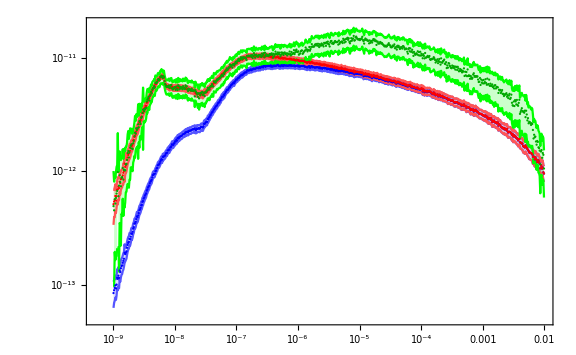

```mathematica
EspecPairs=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]],2];
EspecPairsErrt=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]+6d[[;;,6]]],2];
EspecPairsErrb=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]-6d[[;;,6]]],2];
EndspecPairs=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]],2];
EndspecPairsErrt=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]+6dNoDecay[[;;,6]]],2];
EndspecPairsErrb=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]-6dNoDecay[[;;,6]]],2];
EiispecPairs=Partition[Riffle[dincinb[[;;,4]]/1000,dincinb[[;;,5]]],2];
EiispecPairsErrt=Partition[Riffle[dincinb[[;;,4]]/1000,dincinb[[;;,5]]+6dincinb[[;;,6]]],2];
EiispecPairsErrb=Partition[Riffle[dincinb[[;;,4]]/1000,dincinb[[;;,5]]-6dincinb[[;;,6]]],2];
ListLogLogPlot[
{EspecPairs,EspecPairsErrt,EspecPairsErrb,EndspecPairs,EndspecPairsErrt,EndspecPairsErrb,EiispecPairs,EiispecPairsErrt,EiispecPairsErrb},
ImageSize->Large,Frame->True,Joined->{False,True,True,False,True,True,False,True,True},Filling->{2->{3},5->{6},8->{9}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue],Red,Lighter[Red],Lighter[Red],Darker[Green],Green,Green},GridLines->All,PlotRange->{5 10^-14,2 10^-11}]
```

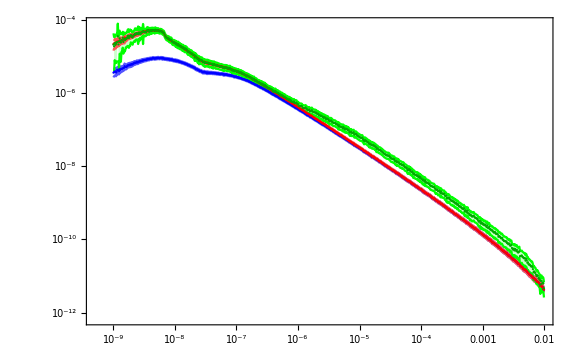

```mathematica
EspecPairs=Partition[Riffle[d[[;;,4]]/1000,d[[;;,5]]/(d[[;;,3]]-d[[;;,2]])],2];
EspecPairsErrt=Partition[Riffle[d[[;;,4]]/1000,(d[[;;,5]]+6d[[;;,6]])/(d[[;;,3]]-d[[;;,2]])],2];
EspecPairsErrb=Partition[Riffle[d[[;;,4]]/1000,(d[[;;,5]]-6d[[;;,6]])/(d[[;;,3]]-d[[;;,2]])],2];
EndspecPairs=Partition[Riffle[dNoDecay[[;;,4]]/1000,dNoDecay[[;;,5]]/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
EndspecPairsErrt=Partition[Riffle[dNoDecay[[;;,4]]/1000,(dNoDecay[[;;,5]]+6dNoDecay[[;;,6]])/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
EndspecPairsErrb=Partition[Riffle[dNoDecay[[;;,4]]/1000,(dNoDecay[[;;,5]]-6dNoDecay[[;;,6]])/(dNoDecay[[;;,3]]-dNoDecay[[;;,2]])],2];
EiispecPairs=Partition[Riffle[dincinb[[;;,4]]/1000,dincinb[[;;,5]]/(dincinb[[;;,3]]-dincinb[[;;,2]])],2];
EiispecPairsErrt=Partition[Riffle[dNoDecay[[;;,4]]/1000,(dincinb[[;;,5]]+6dincinb[[;;,6]])/(dincinb[[;;,3]]-dincinb[[;;,2]])],2];
EiispecPairsErrb=Partition[Riffle[dincinb[[;;,4]]/1000,(dincinb[[;;,5]]-6dincinb[[;;,6]])/(dincinb[[;;,3]]-dincinb[[;;,2]])],2];
ListLogLogPlot[
{EspecPairs,EspecPairsErrt,EspecPairsErrb,EndspecPairs,EndspecPairsErrt,EndspecPairsErrb,EiispecPairs,EiispecPairsErrt,EiispecPairsErrb},
ImageSize->Large,Frame->True,Joined->{False,True,True,False,True,True,False,True,True},Filling->{2->{3},5->{6},8->{9}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue],Red,Lighter[Red],Lighter[Red],Darker[Green],Green,Green},GridLines->All]
```

```mathematica
p0=4.4598`100 10^6;
p1=3.6840`100 10^-8;
p2=4.4183`100 10^5;
p3=0.9181`100;
p4=1.4567`100 10^-7;
p5=5.0338`100;
s[x_]=p0/p1 x ⅇ^(-x/p1)+(p2(x/p4)^p5(p4/x)^p3)/(1+(x/p4)^p5);
AD[x_]=Cos[x]^(5/4);
EePDF[Ee_]=FullSimplify[s[Ee]/NIntegrate[s[Ee],{Ee,10^-9,10^-2},WorkingPrecision->90,AccuracyGoal->20,PrecisionGoal->20]]
AePDF[θ_]=FullSimplify[AD[θ]/NIntegrate[AD[θ],{θ,0,π/2},WorkingPrecision->90,AccuracyGoal->20,PrecisionGoal->20]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ee near {Ee} = {5.7063238008294073156466006414391865388511528162115454113623781646636748130348081119292234700436458438197579319512284902215099005151071792466×10^-7}. NIntegrate obtained 1.3344610093645871403935540714042466190968395051356788117609984285027064013174767147991814862891318014196514687538730814765112251855760555631 and 2.1103863142228105441007414065740519965419487637338683484451812721612365817513300663752071606510474931886214281276510996083051225557510663245×10^-13 for the integral and error estimates.

9.07172491907178396755348082384732845415722023656074800040861900501772392123073231588192615×10^13 ⅇ^(-2.714440825190010857763300760043431053203040173724212812160694896851248642779587404994571118349619978×10^7 Ee) Ee+(4.5442990972019588147496187052277537233204258554897045691209833561745694147011879999948981×10^33 (1/Ee)^0.9181 Ee^5.0338)/(1+2.5955385812264932799677304301611234049501854921236982365409503231874408604901244718921545918507349×10^34 Ee^5.0338)

1.07425917878735074884995016222072182268037256860695708903071702049044345022681759726806329 Cos[θ]^(5/4)

```mathematica
CountIntensities=Table[c[[En,2;;,6]]/Max[c[[En,2;;,6]]],{En,1,Length[c],1}]/(180/5 360/5);
EeIntensities=Table[EePDF[c[[En,2;;,12]]],{En,1,Length[c],1}];
AeIntensities=Table[AePDF[ArcCos[c[[En,2;;,14]]]],{En,1,Length[c],1}];
DIntensities=Table[c[[En,2;;,16]],{En,1,Length[c],1}];
tIntensities=Table[ⅇ^(-c[[En,2;;,10]]/881),{En,1,Length[c],1}];
```

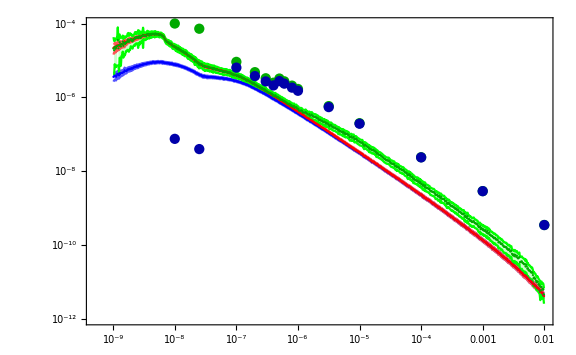

```mathematica
Show[
ListLogLogPlot[{EspecPairs,EspecPairsErrt,EspecPairsErrb,EndspecPairs,EndspecPairsErrt,EndspecPairsErrb,EiispecPairs,EiispecPairsErrt,EiispecPairsErrb},
Joined->{False,True,True,False,True,True,False,True,True},Filling->{2->{3},5->{6},8->{9}},PlotStyle->{Blue,Lighter[Blue],Lighter[Blue],Red,Lighter[Red],Lighter[Red],Darker[Green],Green,Green},
ImageSize->Large,Frame->True,GridLines->All,PlotRange->{10^-12,10^-4}],
ListLogLogPlot[Partition[Riffle[Edetect,Table[Total[CountIntensities[[En]] EeIntensities[[En]] AeIntensities[[En]] DIntensities[[En]]],{En,1,Length[c],1}]],2],PlotStyle->Darker[Green]],ListLogLogPlot[Partition[Riffle[Edetect,Table[Total[CountIntensities[[En]] EeIntensities[[En]] AeIntensities[[En]] DIntensities[[En]]tIntensities[[En]]],{En,1,Length[c],1}]],2],PlotStyle->Darker[Blue]]
]
```

```mathematica
ListLogLogPlot[Partition[Riffle[Edetect,Table[Total[CountIntensities[[En]] EeIntensities[[En]] AeIntensities[[En]] DIntensities[[En]]]tIntensities[[En]],{En,1,Length[c],1}]],2],PlotStyle->Darker[Blue]]
```

-Graphics-